Test suite for the notebook “Semisimple Lie Algebras”, a notebook that calculate those algebras, representations of them, products and powers of those representations, and branching rules: how those representations appear in subalgebras.

To do:

Graphics, extras

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Semisimple Lie Algebras.nb"]
```

## Performance Tests

```mathematica
PTFillArray["Array",n_] := Module[{arr},
arr = {};
Do[AppendTo[arr,i^2],{i,n}];
arr]
```

```mathematica
PTFillArray["Function",n_] := Module[{f},
Do[f[i] = i^2,{i,n}];
f /@ Range[n]
]
```

```mathematica
PTFillArray["Association",n_] := Module[{arr,a},
a = <||>;
Do[AssociateTo[a,i->i^2],{i,n}];
Lookup[a,Range[n]]
]
```

```mathematica
PTReplaceArray["Array",arr_] := Module[{n,newarr},
n = Length[arr];
newarr = ConstantArray[0,n];
Do[newarr[[i]] = arr[[i]],{i,n}];
newarr
]
```

```mathematica
PTReplaceArray["Function",arr_] := Module[{n,f},
n = Length[arr];
Do[f[i]=0,{i,n}];
Do[f[i] = arr[[i]],{i,n}];
f /@ Range[n]
]
```

```mathematica
PTReplaceArray["Association",arr_] := Module[{n,a},
a = <||>;
n = Length[arr];
Do[AssociateTo[a,i->0],{i,n}];
Do[a[i] = arr[[i]],{i,n}];
Lookup[a,Range[n]]
]
```

## Lie Algebras themselves

### Dynkin diagrams

#### Input-error checking

```mathematica
Off[General::stop]
```

```mathematica
MakeDynkinDiagram /@ {1.2,{1},{1,1,1},{8,1},{1,0},{2,0},{3,0},{4,1},{5,2},{6,3},{6,5},{7,1},{7,3}}
```

LieAlgebra::badtype: Invalid algebra type: 1.2

LieAlgebra::badtype: Invalid algebra type: {1}

LieAlgebra::badtype: Invalid algebra type: {1,1,1}

LieAlgebra::badtype: Invalid algebra type: {8,1}

LieAlgebra::badtype: Invalid algebra type: {1,0}

LieAlgebra::badtype: Invalid algebra type: {2,0}

LieAlgebra::badtype: Invalid algebra type: {3,0}

LieAlgebra::badtype: Invalid algebra type: {4,1}

LieAlgebra::badtype: Invalid algebra type: {5,2}

LieAlgebra::badtype: Invalid algebra type: {6,3}

LieAlgebra::badtype: Invalid algebra type: {6,5}

LieAlgebra::badtype: Invalid algebra type: {7,1}

LieAlgebra::badtype: Invalid algebra type: {7,3}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
On[General::stop]
```

#### Dumps of diagram data

```mathematica
Table[MakeDynkinDiagram[{1,n}],{n,6}] // TableForm
```

1 | 
1
1 | 1 | 2 | 1
1
1
1 | 1 | 2 | 1
2 | 3 | 1
1
1
1
1 | 1 | 2 | 1
2 | 3 | 1
3 | 4 | 1
1
1
1
1
1 | 1 | 2 | 1
2 | 3 | 1
3 | 4 | 1
4 | 5 | 1
1
1
1
1
1
1 | 1 | 2 | 1
2 | 3 | 1
3 | 4 | 1
4 | 5 | 1
5 | 6 | 1

```mathematica
Table[MakeDynkinDiagram[{2,n}],{n,6}] // TableForm
```

1 | 
2
1 | 1 | 2 | 2
2
2
1 | 1 | 2 | 2
2 | 3 | 2
2
2
2
1 | 1 | 2 | 2
2 | 3 | 2
3 | 4 | 2
2
2
2
2
1 | 1 | 2 | 2
2 | 3 | 2
3 | 4 | 2
4 | 5 | 2
2
2
2
2
2
1 | 1 | 2 | 2
2 | 3 | 2
3 | 4 | 2
4 | 5 | 2
5 | 6 | 2

```mathematica
Table[MakeDynkinDiagram[{3,n}],{n,6}] // TableForm
```

1 | 
1
2 | 1 | 2 | 2
1
1
2 | 1 | 2 | 1
2 | 3 | 2
1
1
1
2 | 1 | 2 | 1
2 | 3 | 1
3 | 4 | 2
1
1
1
1
2 | 1 | 2 | 1
2 | 3 | 1
3 | 4 | 1
4 | 5 | 2
1
1
1
1
1
2 | 1 | 2 | 1
2 | 3 | 1
3 | 4 | 1
4 | 5 | 1
5 | 6 | 2

```mathematica
Table[MakeDynkinDiagram[{4,n}],{n,2,6}] // TableForm
```

1
1 | 
1
1
1 | 1 | 2 | 1
1 | 3 | 1
1
1
1
1 | 1 | 2 | 1
2 | 3 | 1
2 | 4 | 1
1
1
1
1
1 | 1 | 2 | 1
2 | 3 | 1
3 | 4 | 1
3 | 5 | 1
1
1
1
1
1
1 | 1 | 2 | 1
2 | 3 | 1
3 | 4 | 1
4 | 5 | 1
4 | 6 | 1

```mathematica
Table[MakeDynkinDiagram[{5,n}],{n,3,8}] // TableForm
```

1
1
1 | 1 | 2 | 1
1
1
1
1 | 1 | 2 | 1
2 | 3 | 1
3 | 4 | 1
1
1
1
1
1 | 1 | 2 | 1
2 | 3 | 1
3 | 4 | 1
3 | 5 | 1
1
1
1
1
1
1 | 1 | 2 | 1
2 | 3 | 1
3 | 4 | 1
4 | 5 | 1
3 | 6 | 1
1
1
1
1
1
1
1 | 1 | 2 | 1
2 | 3 | 1
3 | 4 | 1
4 | 5 | 1
5 | 6 | 1
3 | 7 | 1
1
1
1
1
1
1
1
1 | 1 | 2 | 1
2 | 3 | 1
3 | 4 | 1
4 | 5 | 1
5 | 6 | 1
6 | 7 | 1
3 | 8 | 1

```mathematica
{MakeDynkinDiagram[{6,4}]}// TableForm
```

2
2
1
1 | 1 | 2 | 2
2 | 3 | 2
3 | 4 | 1

```mathematica
{MakeDynkinDiagram[{7,2}]}// TableForm
```

3
1 | 1 | 2 | 3

#### Display of diagrams

```mathematica
(* From "Extras" *)
```

```mathematica
ShowDDGraf[type_] := {type,GraphDynkDiag[MakeDynkinDiagram[type]]}
```

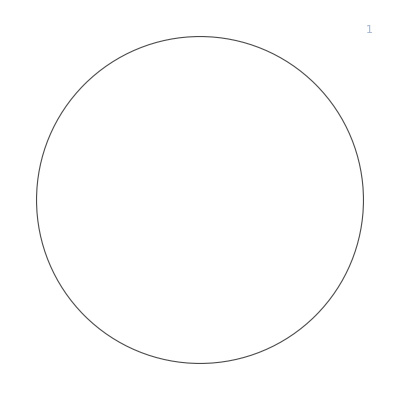
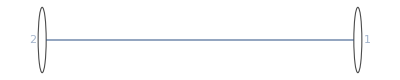
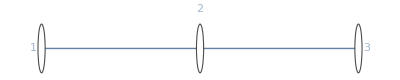
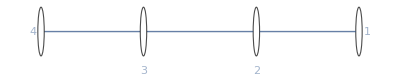
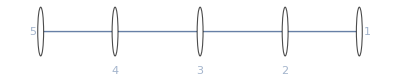
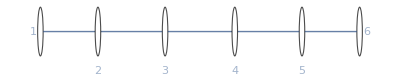
{{{1,1},-Graphics-},{{1,2},-Graphics-},{{1,3},-Graphics-},{{1,4},-Graphics-},{{1,5},-Graphics-},{{1,6},-Graphics-}}

```mathematica
Table[ShowDDGraf[{1,n}],{n,6}]
```

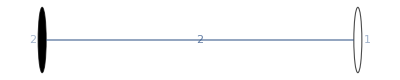
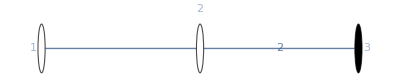
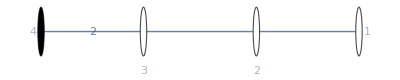
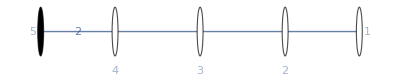
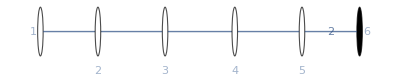
{{{2,1},-Graphics-},{{2,2},-Graphics-},{{2,3},-Graphics-},{{2,4},-Graphics-},{{2,5},-Graphics-},{{2,6},-Graphics-}}

```mathematica
Table[ShowDDGraf[{2,n}],{n,6}]
```

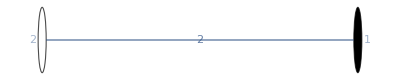
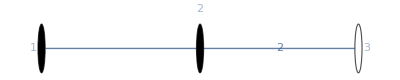
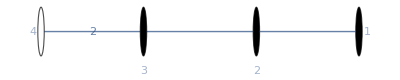
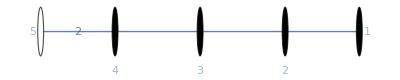
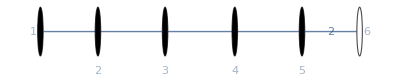
{{{3,1},-Graphics-},{{3,2},-Graphics-},{{3,3},-Graphics-},{{3,4},-Graphics-},{{3,5},-Graphics-},{{3,6},-Graphics-}}

```mathematica
Table[ShowDDGraf[{3,n}],{n,6}]
```

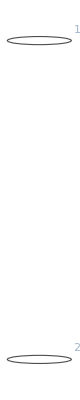
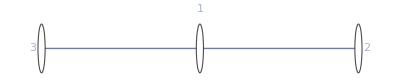
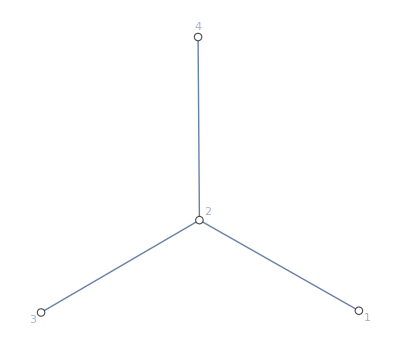
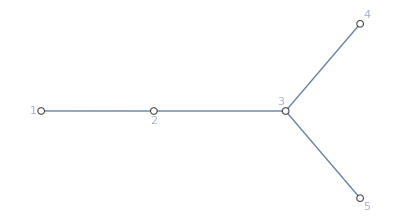
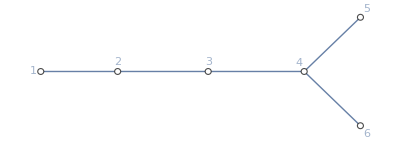
{{{4,2},-Graphics-},{{4,3},-Graphics-},{{4,4},-Graphics-},{{4,5},-Graphics-},{{4,6},-Graphics-}}

```mathematica
Table[ShowDDGraf[{4,n}],{n,2,6}]
```

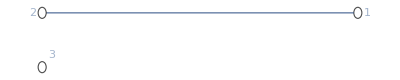
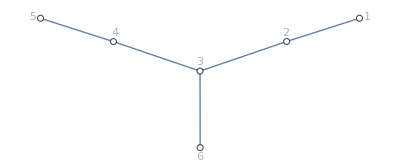
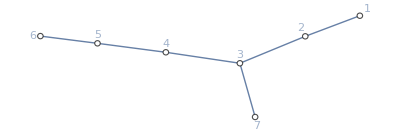
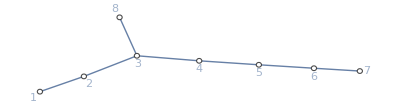
{{{5,3},-Graphics-},{{5,4},-Graphics-},{{5,5},-Graphics-},{{5,6},-Graphics-},{{5,7},-Graphics-},{{5,8},-Graphics-}}

```mathematica
Table[ShowDDGraf[{5,n}],{n,3,8}]
```

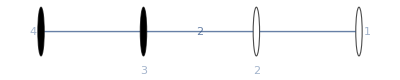
{{{6,4},-Graphics-}}

```mathematica
Table[ShowDDGraf[{6,n}],{n,4,4}]
```

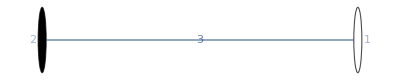
{{{7,2},-Graphics-}}

```mathematica
Table[ShowDDGraf[{7,n}],{n,2,2}]
```

### Matrices

```mathematica
(* Metric and Cartan matrix *)
```

```mathematica
ShowMats[type_] := Block[{dd},
dd = MakeDynkinDiagram[type];
Prepend[MatrixForm /@ {MakeMetric[dd],MakeCartanMatrix[dd]},type]
]
```

```mathematica
ShowMats/@ {{1,5},{2,5},{3,5},{4,5},{7,2},{6,4},{5,6},{5,8}}
```

{{{1,5},(2 | -1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | 0
0 | 0 | -1 | 2 | -1
0 | 0 | 0 | -1 | 2),(2 | -1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | 0
0 | 0 | -1 | 2 | -1
0 | 0 | 0 | -1 | 2)},{{2,5},(4 | -2 | 0 | 0 | 0
-2 | 4 | -2 | 0 | 0
0 | -2 | 4 | -2 | 0
0 | 0 | -2 | 4 | -2
0 | 0 | 0 | -2 | 2),(2 | -1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | 0
0 | 0 | -1 | 2 | -2
0 | 0 | 0 | -1 | 2)},{{3,5},(2 | -1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | 0
0 | 0 | -1 | 2 | -2
0 | 0 | 0 | -2 | 4),(2 | -1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | 0
0 | 0 | -1 | 2 | -1
0 | 0 | 0 | -2 | 2)},{{4,5},(2 | -1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | -1
0 | 0 | -1 | 2 | 0
0 | 0 | -1 | 0 | 2),(2 | -1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | -1
0 | 0 | -1 | 2 | 0
0 | 0 | -1 | 0 | 2)},{{7,2},(6 | -3
-3 | 2),(2 | -3
-1 | 2)},{{6,4},(4 | -2 | 0 | 0
-2 | 4 | -2 | 0
0 | -2 | 2 | -1
0 | 0 | -1 | 2),(2 | -1 | 0 | 0
-1 | 2 | -2 | 0
0 | -1 | 2 | -1
0 | 0 | -1 | 2)},{{5,6},(2 | -1 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | -1
0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | -1 | 2 | 0
0 | 0 | -1 | 0 | 0 | 2),(2 | -1 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | -1
0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | -1 | 2 | 0
0 | 0 | -1 | 0 | 0 | 2)},{{5,8},(2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0 | 0 | -1
0 | 0 | -1 | 2 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 2 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 2),(2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0 | 0 | -1
0 | 0 | -1 | 2 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 2 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 2)}}

```mathematica
GetLieAlgebra[{3,5}]["Metric"] // MatrixForm
```

(2 | -1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | 0
0 | 0 | -1 | 2 | -2
0 | 0 | 0 | -2 | 4)

```mathematica
GetLieAlgebra[{3,5}]["CtnMat"] // MatrixForm
```

(2 | -1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | 0
0 | 0 | -1 | 2 | -1
0 | 0 | 0 | -2 | 2)

### Algebras

```mathematica
ResetLieAlgebras[]
```

<||>

```mathematica
MakeLieAlgebra[{1,2}]
```

<|Type→{1,2},Name→A2 SU(3),DynkDiag→{{1,1},{{1,2,1}}},Metric→{{2,-1},{-1,2}},InvMet→{{2/3,1/3},{1/3,2/3}},CtnMat→{{2,-1},{-1,2}},InvCtn→{{2/3,1/3},{1/3,2/3}},PosRoots→{{{0,1},{-1,2}},{{1,0},{2,-1}},{{1,1},{1,1}}}|>

```mathematica
MakeLieAlgebra[{2,2}]
```

<|Type→{2,2},Name→B2 SO(5),DynkDiag→{{2,1},{{1,2,2}}},Metric→{{4,-2},{-2,2}},InvMet→{{1/2,1/2},{1/2,1}},CtnMat→{{2,-2},{-1,2}},InvCtn→{{1,1},{1/2,1}},PosRoots→{{{0,1},{-1,2}},{{1,0},{2,-2}},{{1,1},{1,0}},{{1,2},{0,2}}}|>

```mathematica
MakeLieAlgebra[{3,2}]
```

<|Type→{3,2},Name→C2 Sp(4),DynkDiag→{{1,2},{{1,2,2}}},Metric→{{2,-2},{-2,4}},InvMet→{{1,1/2},{1/2,1/2}},CtnMat→{{2,-1},{-2,2}},InvCtn→{{1,1/2},{1,1}},PosRoots→{{{0,1},{-2,2}},{{1,0},{2,-1}},{{1,1},{0,1}},{{2,1},{2,0}}}|>

```mathematica
MakeLieAlgebra[{4,2}]
```

<|Type→{4,2},Name→D2 SO(4),DynkDiag→{{1,1},{}},Metric→{{2,0},{0,2}},InvMet→{{1/2,0},{0,1/2}},CtnMat→{{2,0},{0,2}},InvCtn→{{1/2,0},{0,1/2}},PosRoots→{{{0,1},{0,2}},{{1,0},{2,0}}}|>

```mathematica
MakeLieAlgebra[{7,2}]
```

<|Type→{7,2},Name→G2 ,DynkDiag→{{3,1},{{1,2,3}}},Metric→{{6,-3},{-3,2}},InvMet→{{2/3,1},{1,2}},CtnMat→{{2,-3},{-1,2}},InvCtn→{{2,3},{1,2}},PosRoots→{{{0,1},{-1,2}},{{1,0},{2,-3}},{{1,1},{1,-1}},{{1,2},{0,1}},{{1,3},{-1,3}},{{2,3},{1,0}}}|>

### Dimensions

```mathematica
Table[AlgDimension[{1,n}]-n(n+2),{n,1,10}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[AlgDimension[{2,n}]-n(2n+1),{n,1,10}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[AlgDimension[{3,n}]-n(2n+1),{n,1,10}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[AlgDimension[{4,n}]-n(2n-1),{n,2,10}]
```

{0,0,0,0,0,0,0,0,0}

```mathematica
Join[{AlgDimension[{1,1}]+AlgDimension[{1,2}],AlgDimension[{1,4}],AlgDimension[{4,5}]},Table[AlgDimension[{5,n}],{n,6,8}]]
```

{11,24,45,78,133,248}

```mathematica
NestList[Differences,%,6]
```

{{11,24,45,78,133,248},{13,21,33,55,115},{8,12,22,60},{4,10,38},{6,28},{22},{}}

## Irreps - Irreducible Representations

### Weyl-group orders

```mathematica
(* For showing what is feasible in finding Weyl orbit using orthgonal root bases *)
```

```mathematica
(* Exceptional family E *)
```

```mathematica
{#,WeylGroupOrder[{5,#}]}& /@ Range[3,8]
```

{{3,12},{4,120},{5,1920},{6,51840},{7,2903040},{8,696729600}}

```mathematica
(* Exceptional: relation to subalgebras' orders *)
```

```mathematica
WeylGroupOrder[{7,2}]/WeylGroupOrder[{1,2}]
```

2

```mathematica
WeylGroupOrder[{6,4}]/WeylGroupOrder[{2,4}]
```

3

```mathematica
Table[{n,WeylGroupOrder[{5,n}]/{WeylGroupOrder[{1,n-1}],WeylGroupOrder[{4,n-1}]}},{n,6,8}]
```

{{6,{72,27}},{7,{576,126}},{8,{17280,2160}}}

### Weyl orbits

```mathematica
OrbitTimingVerify[{1,4},10^(Range[4]-1)]
```

{{WGGens,DomWt,Explicit},{0.032943,0.012308,0.002014},{{True,True,True},{True,True,True},{True,True,True}}}

```mathematica
OrbitTimingVerify[{2,4},10^(Range[4]-1)]
```

{{WGGens,DomWt,Explicit},{0.015066,0.006846,0.005038},{{True,True,True},{True,True,True},{True,True,True}}}

```mathematica
OrbitTimingVerify[{3,4},10^(Range[4]-1)]
```

{{WGGens,DomWt,Explicit},{0.058926,0.037624,0.007037},{{True,True,True},{True,True,True},{True,True,True}}}

```mathematica
OrbitTimingVerify[{4,4},10^(Range[4]-1)]
```

{{WGGens,DomWt,Explicit},{0.02586,0.018676,0.00462},{{True,True,True},{True,True,True},{True,True,True}}}

```mathematica
OrbitTimingVerify[{6,4},10^(Range[4]-1)]
```

{{WGGens,DomWt,Explicit},{0.069087,0.02041,0.012466},{{True,True,True},{True,True,True},{True,True,True}}}

```mathematica
OrbitTimingVerify[{7,2},10^(Range[2]-1)]
```

{{WGGens,DomWt,Explicit},{0.001329,0.000304,0.000205},{{True,True,True},{True,True,True},{True,True,True}}}

```mathematica
OrbitTimingVerify[{1,4},Array[w,4],False]
```

{{WGGens,Explicit},{0.070433,0.015295},{{True,True},{True,True}}}

```mathematica
OrbitTimingVerify[{2,4},Array[w,4],False]
```

{{WGGens,Explicit},{0.115879,0.033261},{{True,True},{True,True}}}

```mathematica
OrbitTimingVerify[{3,4},Array[w,4],False]
```

{{WGGens,Explicit},{0.115516,0.040518},{{True,True},{True,True}}}

```mathematica
OrbitTimingVerify[{4,4},Array[w,4],False]
```

{{WGGens,Explicit},{0.046814,0.02051},{{True,True},{True,True}}}

```mathematica
OrbitTimingVerify[{6,4},Array[w,4],False]
```

{{WGGens,Explicit},{0.480257,0.149566},{{True,True},{True,True}}}

```mathematica
OrbitTimingVerify[{7,2},Array[w,2],False]
```

{{WGGens,Explicit},{0.001498,0.000535},{{True,True},{True,True}}}

```mathematica
MakeOrbit[{7,2},{1,0},"WGGens"]
```

{{{2,3},{1,0}},{{1,3},{-1,3}},{{1,0},{2,-3}},{{-1,0},{-2,3}},{{-1,-3},{1,-3}},{{-2,-3},{-1,0}}}

```mathematica
MakeOrbit[{7,2},{1,0},"DomWt"]
```

{{{2,3},{1,0}},{{1,3},{-1,3}},{{1,0},{2,-3}},{{-1,0},{-2,3}},{{-1,-3},{1,-3}},{{-2,-3},{-1,0}}}

```mathematica
MakeOrbit[{7,2},{1,0},"Explicit"]
```

{{{2,3},{1,0}},{{1,3},{-1,3}},{{1,0},{2,-3}},{{-1,0},{-2,3}},{{-1,-3},{1,-3}},{{-2,-3},{-1,0}}}

```mathematica
MakeOrbit[{7,2},{0,1},"Explicit"]
```

{{{1,2},{0,1}},{{1,1},{1,-1}},{{0,1},{-1,2}},{{0,-1},{1,-2}},{{-1,-1},{-1,1}},{{-1,-2},{0,-1}}}

```mathematica
MakeOrbit[{7,2},{1,1},"Explicit"]
```

{{{3,5},{1,1}},{{2,5},{-1,4}},{{3,4},{2,-1}},{{1,4},{-2,5}},{{2,1},{3,-4}},{{-1,1},{-3,5}},{{1,-1},{3,-5}},{{-2,-1},{-3,4}},{{-1,-4},{2,-5}},{{-3,-4},{-2,1}},{{-2,-5},{1,-4}},{{-3,-5},{-1,-1}}}

```mathematica
OrbitDomWtFromRoot[{7,2},{-1,0}]
```

{{2,3},{1,0}}

```mathematica
OrbitDomWtFromRoot[{7,2},{-1,-1}]
```

{{1,2},{0,1}}

```mathematica
OrbitDomWtFromRoot[{7,2},{-1,-2}]
```

{{1,2},{0,1}}

```mathematica
OrbitDomWtFromRoot[{7,2},{-1,-3}]
```

{{2,3},{1,0}}

```mathematica
OrbitDomWtFromRoot[{7,2},{-1,-4}]
```

{{3,5},{1,1}}

```mathematica
OrbitDomWtFromRoot[{7,2},{-1,-4}]
```

{{3,5},{1,1}}

### Irreps themselves

```mathematica
RepsVerifyTiming[{1,4},{0,0,1,2}]
```

{0.011335,0.011729,True}

```mathematica
RepsVerifyTiming[{2,4},{0,0,1,2}]
```

{0.0893,0.040488,True}

```mathematica
RepsVerifyTiming[{3,4},{0,0,1,2}]
```

{0.372816,0.134108,True}

```mathematica
RepsVerifyTiming[{4,4},{0,0,1,2}]
```

{0.021786,0.01737,True}

```mathematica
RepsVerifyTiming[{6,4},{0,0,1,2}]
```

{0.342006,0.113682,True}

```mathematica
RepsVerifyTiming[{7,2},{1,2}]
```

{0.004464,0.008371,True}

```mathematica
RepsVerifyTiming[{5,6},{1,0,0,0,1,0}]
```

{0.065139,0.025844,True}

### Conjugate irreps

```mathematica
RepConjugate[{1,4},Array[w,4]] == Reverse[Array[w,4]]
```

True

```mathematica
RepConjugate[{2,4},Array[w,4]] == Array[w,4]
```

True

```mathematica
RepConjugate[{3,4},Array[w,4]] == Array[w,4]
```

True

```mathematica
RepConjugate[{4,4},Array[w,4]]
```

{w[1],w[2],w[4],w[3]}

```mathematica
RepConjugate[{5,6},Array[w,6]]
```

{w[5],w[4],w[3],w[2],w[1],w[6]}

```mathematica
RepConjugate[{5,7},Array[w,7]] == Array[w,7]
```

True

```mathematica
RepConjugate[{5,8},Array[w,8]] == Array[w,8]
```

True

```mathematica
RepConjugate[{6,4},Array[w,4]] == Array[w,4]
```

True

```mathematica
RepConjugate[{7,2},Array[w,2]] == Array[w,2]
```

True

```mathematica
RepConjugateD4[Array[w,4],{2,3,1}]
```

{w[3],w[2],w[4],w[1]}

```mathematica
RepConjugateD4[Array[w,4],{2,1,3}]
```

{w[3],w[2],w[1],w[4]}

### Properties

#### Total degeneracy

```mathematica
TotalDegenTest[{#,4},{2,1,0,1}]& /@ {1,2,3,4,6}
```

{True,True,True,True,True}

```mathematica
RepHeightMultTest[{#,4}]& /@ Range[4]
```

{True,True,True,True}

```mathematica
Table[TotalDegenBasic[{f,6}],{f,1,4}]
```

{{7,21,35,35,21,7},{13,78,286,715,1287,64},{12,65,208,429,572,429},{12,66,220,495,32,32}}

```mathematica
ExceptionalTypes = {{7,2},{6,4},{5,6},{5,7},{5,8}};
```

```mathematica
RepHeightMultTest /@ ExceptionalTypes
```

{True,True,True,True,True}

```mathematica
Table[TotalDegenBasic[ex],{ex,ExceptionalTypes}]
```

{{14,7},{52,1274,273,26},{27,351,2925,351,27,78},{133,8645,365750,27664,1539,56,912},{3875,6696000,6899079264,146325270,2450240,30380,248,147250}}

#### Tables of properties

```mathematica
bsrtop[type_,op_] := op[type,#]& /@ IdentityMatrix[type[[2]]]
```

```mathematica
bsrtrl[type_] := bsrtop[type,RepReality]
```

```mathematica
bsrtpp[type_] := bsrtop[type,RepProperties]
```

```mathematica
(* First vertical: rank, first horizontal: which root 1 and not 0, second vertical: reality, congruence moduli, congruence values, second horizontal: which congruence modulus and value *)
```

```mathematica
TableForm[Table[bsrtpp[{1,k}],{k,8}],TableHeadings->{{1,#}& /@ Range[8],Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
{1,1} | -1
2
1 |  |  |  |  |  |  | 
{1,2} | 0
3
1 | 0
3
2 |  |  |  |  |  | 
{1,3} | 0
4
1 | 1
4
2 | 0
4
3 |  |  |  |  | 
{1,4} | 0
5
1 | 0
5
2 | 0
5
3 | 0
5
4 |  |  |  | 
{1,5} | 0
6
1 | 0
6
2 | -1
6
3 | 0
6
4 | 0
6
5 |  |  | 
{1,6} | 0
7
1 | 0
7
2 | 0
7
3 | 0
7
4 | 0
7
5 | 0
7
6 |  | 
{1,7} | 0
8
1 | 0
8
2 | 0
8
3 | 1
8
4 | 0
8
5 | 0
8
6 | 0
8
7 | 
{1,8} | 0
9
1 | 0
9
2 | 0
9
3 | 0
9
4 | 0
9
5 | 0
9
6 | 0
9
7 | 0
9
8

```mathematica
TableForm[Table[bsrtpp[{2,k}],{k,8}],TableHeadings->{{2,#}& /@ Range[8],Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
{2,1} | -1
2
1 |  |  |  |  |  |  | 
{2,2} | 1
2
0 | -1
2
1 |  |  |  |  |  | 
{2,3} | 1
2
0 | 1
2
0 | 1
2
1 |  |  |  |  | 
{2,4} | 1
2
0 | 1
2
0 | 1
2
0 | 1
2
1 |  |  |  | 
{2,5} | 1
2
0 | 1
2
0 | 1
2
0 | 1
2
0 | -1
2
1 |  |  | 
{2,6} | 1
2
0 | 1
2
0 | 1
2
0 | 1
2
0 | 1
2
0 | -1
2
1 |  | 
{2,7} | 1
2
0 | 1
2
0 | 1
2
0 | 1
2
0 | 1
2
0 | 1
2
0 | 1
2
1 | 
{2,8} | 1
2
0 | 1
2
0 | 1
2
0 | 1
2
0 | 1
2
0 | 1
2
0 | 1
2
0 | 1
2
1

```mathematica
TableForm[Table[bsrtpp[{3,k}],{k,8}],TableHeadings->{{3,#}& /@ Range[8],Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
{3,1} | -1
2
1 |  |  |  |  |  |  | 
{3,2} | -1
2
1 | 1
2
0 |  |  |  |  |  | 
{3,3} | -1
2
1 | 1
2
0 | -1
2
1 |  |  |  |  | 
{3,4} | -1
2
1 | 1
2
0 | -1
2
1 | 1
2
0 |  |  |  | 
{3,5} | -1
2
1 | 1
2
0 | -1
2
1 | 1
2
0 | -1
2
1 |  |  | 
{3,6} | -1
2
1 | 1
2
0 | -1
2
1 | 1
2
0 | -1
2
1 | 1
2
0 |  | 
{3,7} | -1
2
1 | 1
2
0 | -1
2
1 | 1
2
0 | -1
2
1 | 1
2
0 | -1
2
1 | 
{3,8} | -1
2
1 | 1
2
0 | -1
2
1 | 1
2
0 | -1
2
1 | 1
2
0 | -1
2
1 | 1
2
0

```mathematica
TableForm[Table[bsrtpp[{4,k}],{k,2,8}],TableHeadings->{{4,#}& /@ Range[2,8],Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
{4,2} | 0 |  | 
2 | 2 | 2
1 | 1 | 0 | 0 |  | 
2 | 2 | 2
1 | 0 | 1 |  |  |  |  |  | 
{4,3} | 1 | 
2 | 4
0 | 2 | 0 | 
2 | 4
1 | 1 | 0 | 
2 | 4
1 | 3 |  |  |  |  | 
{4,4} | 1 |  | 
2 | 2 | 2
0 | 1 | 1 | 1 |  | 
2 | 2 | 2
0 | 0 | 0 | 0 |  | 
2 | 2 | 2
1 | 1 | 0 | 0 |  | 
2 | 2 | 2
1 | 0 | 1 |  |  |  | 
{4,5} | 1 | 
2 | 4
0 | 2 | 1 | 
2 | 4
0 | 0 | 1 | 
2 | 4
0 | 2 | 0 | 
2 | 4
1 | 1 | 0 | 
2 | 4
1 | 3 |  |  | 
{4,6} | 1 |  | 
2 | 2 | 2
0 | 1 | 1 | 1 |  | 
2 | 2 | 2
0 | 0 | 0 | 1 |  | 
2 | 2 | 2
0 | 1 | 1 | 1 |  | 
2 | 2 | 2
0 | 0 | 0 | 0 |  | 
2 | 2 | 2
1 | 1 | 0 | 0 |  | 
2 | 2 | 2
1 | 0 | 1 |  | 
{4,7} | 1 | 
2 | 4
0 | 2 | 1 | 
2 | 4
0 | 0 | 1 | 
2 | 4
0 | 2 | 1 | 
2 | 4
0 | 0 | 1 | 
2 | 4
0 | 2 | 0 | 
2 | 4
1 | 1 | 0 | 
2 | 4
1 | 3 | 
{4,8} | 1 |  | 
2 | 2 | 2
0 | 1 | 1 | 1 |  | 
2 | 2 | 2
0 | 0 | 0 | 1 |  | 
2 | 2 | 2
0 | 1 | 1 | 1 |  | 
2 | 2 | 2
0 | 0 | 0 | 1 |  | 
2 | 2 | 2
0 | 1 | 1 | 1 |  | 
2 | 2 | 2
0 | 0 | 0 | 0 |  | 
2 | 2 | 2
1 | 1 | 0 | 0 |  | 
2 | 2 | 2
1 | 0 | 1

```mathematica
TableForm[bsrtpp /@ ExceptionalTypes,TableHeadings->{ExceptionalTypes,Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
{7,2} | 1

 | 1

 |  |  |  |  |  | 
{6,4} | 1

 | 1

 | 1

 | 1

 |  |  |  | 
{5,6} | 0
3
1 | 0
3
2 | 1
3
0 | 0
3
1 | 0
3
2 | 1
3
0 |  | 
{5,7} | 1
2
0 | 1
2
0 | 1
2
0 | -1
2
1 | 1
2
0 | -1
2
1 | -1
2
1 | 
{5,8} | 1

 | 1

 | 1

 | 1

 | 1

 | 1

 | 1

 | 1

#### QM Angular Momentum

```mathematica
Clear[j,j1,j2] (* Will use them for symbolic versions *)
```

```mathematica
(* Quantum-mechanical angular momentum j: (integer)/2 *)
```

```mathematica
TotalDegen[{1,1},{2j},False] // Simplify
```

1+2 j

```mathematica
CasimirInvariant[{1,1},{2j},False] // Simplify
```

2 j (1+j)

```mathematica
RepIndex[{1,1},{2j},False] // Simplify
```

2/3 j (1+j) (1+2 j)

```mathematica
(* Sum rule for rep products, from R. Slansky, Group theory for model building, p. 36 *)
```

```mathematica
(TotalDegen[{1,1},{2j1},False]*RepIndex[{1,1},{2j2},False] + TotalDegen[{1,1},{2j2},False]*RepIndex[{1,1},{2j1},False]) - Sum[RepIndex[{1,1},{2j},False],{j,j1-j2,j1+j2}] // Simplify
```

0

## Combinations, Products, and Powers

### Combinations

```mathematica
(* Single irrep, list of irreps, counted list of irreps *)
```

```mathematica
GetRep[{1,2},{0,1}]
```

{{1,{1/3,2/3},{0,1}},{1,{1/3,-1/3},{1,-1}},{1,{-2/3,-1/3},{-1,0}}}

```mathematica
GetRepXtnd[{1,2},"Sngl",{2,0}]
```

{{1,{4/3,2/3},{2,0}},{1,{1/3,2/3},{0,1}},{1,{-2/3,2/3},{-2,2}},{1,{1/3,-1/3},{1,-1}},{1,{-2/3,-1/3},{-1,0}},{1,{-2/3,-4/3},{0,-2}}}

```mathematica
GetRepXtnd[{1,2},"List",{{2,0},{0,1}}]
```

{{1,{4/3,2/3},{2,0}},{2,{1/3,2/3},{0,1}},{1,{-2/3,2/3},{-2,2}},{2,{1/3,-1/3},{1,-1}},{2,{-2/3,-1/3},{-1,0}},{1,{-2/3,-4/3},{0,-2}}}

```mathematica
GetRepXtnd[{1,2},"Cntd",{{1,{2,0}},{2,{0,1}}}]
```

{{1,{4/3,2/3},{2,0}},{3,{1/3,2/3},{0,1}},{1,{-2/3,2/3},{-2,2}},{3,{1/3,-1/3},{1,-1}},{3,{-2/3,-1/3},{-1,0}},{1,{-2/3,-4/3},{0,-2}}}

```mathematica
(* Reps from orbits *)
```

```mathematica
GetRepOrbits[{1,2},{1,1}]
```

{{1,{1,1},{1,1}},{2,{0,0},{0,0}}}

```mathematica
RepsFromOrbits[{1,2},{{2,{1,1},{1,1}},{7,{0,0},{0,0}}}]
```

{{2,{1,1}},{3,{0,0}}}

```mathematica
(* Making counted lists from singles, plain lists *)
```

```mathematica
MakeCountedList["Sngl","mem"]
```

{1,mem}

```mathematica
MakeCountedList["List",{"mem1","mem2","mem3"}]
```

{{1,mem1},{1,mem2},{1,mem3}}

```mathematica
MakeCountedList["Cntd",{{1,"mem1"},{2,"mem2"},{3,"mem3"}}]
```

{{1,mem1},{2,mem2},{3,mem3}}

```mathematica
(* Irrep of an algebra product *)
```

```mathematica
GetAlgProdRep[{{1,1},{1,2}},{{1},{1,0}}]
```

{{1,{{1/2},{2/3,1/3}},{{1},{1,0}}},{1,{{1/2},{-1/3,1/3}},{{1},{-1,1}}},{1,{{1/2},{-1/3,-2/3}},{{1},{0,-1}}},{1,{{-1/2},{2/3,1/3}},{{-1},{1,0}}},{1,{{-1/2},{-1/3,1/3}},{{-1},{-1,1}}},{1,{{-1/2},{-1/3,-2/3}},{{-1},{0,-1}}}}

```mathematica
GetAlgProdRepXtnd[{{1,1},{1,2}},"Sngl",{{1},{1,0}}]
```

{{1,{{1/2},{2/3,1/3}},{{1},{1,0}}},{1,{{1/2},{-1/3,1/3}},{{1},{-1,1}}},{1,{{1/2},{-1/3,-2/3}},{{1},{0,-1}}},{1,{{-1/2},{2/3,1/3}},{{-1},{1,0}}},{1,{{-1/2},{-1/3,1/3}},{{-1},{-1,1}}},{1,{{-1/2},{-1/3,-2/3}},{{-1},{0,-1}}}}

```mathematica
GetAlgProdRepXtnd[{{1,1},{1,2}},"List",{{{1},{1,0}}}]
```

{{1,{{1/2},{2/3,1/3}},{{1},{1,0}}},{1,{{1/2},{-1/3,1/3}},{{1},{-1,1}}},{1,{{1/2},{-1/3,-2/3}},{{1},{0,-1}}},{1,{{-1/2},{2/3,1/3}},{{-1},{1,0}}},{1,{{-1/2},{-1/3,1/3}},{{-1},{-1,1}}},{1,{{-1/2},{-1/3,-2/3}},{{-1},{0,-1}}}}

```mathematica
GetAlgProdRepXtnd[{{1,1},{1,2}},"Cntd",{{1,{{1},{1,0}}}}]
```

{{1,{{1/2},{2/3,1/3}},{{1},{1,0}}},{1,{{1/2},{-1/3,1/3}},{{1},{-1,1}}},{1,{{1/2},{-1/3,-2/3}},{{1},{0,-1}}},{1,{{-1/2},{2/3,1/3}},{{-1},{1,0}}},{1,{{-1/2},{-1/3,1/3}},{{-1},{-1,1}}},{1,{{-1/2},{-1/3,-2/3}},{{-1},{0,-1}}}}

```mathematica
(* Empty algebra product - all U(1) factors *)
```

```mathematica
GetAlgProdRep[{},{1,2,3}]
```

{{1,{1,2,3},{1,2,3}}}

### Products

```mathematica
DecomposeRepProduct[{1,2},{1,0},{1,0}]
```

{{1,{2,0}},{1,{0,1}}}

```mathematica
DecomposeRepProduct[{1,2},{1,0},{0,1}]
```

{{1,{1,1}},{1,{0,0}}}

```mathematica
DecomposeRepProduct[{1,2},{1,0},{1,1}]
```

{{1,{2,1}},{1,{0,2}},{1,{1,0}}}

```mathematica
DecomposeRepProductXtnd[{1,2},"Sngl",{1,0},"List",{{1,1},{0,0}}]
```

{{1,{2,1}},{1,{0,2}},{2,{1,0}}}

```mathematica
DecomposeRepProductXtnd[{1,2},"Sngl",{1,0},"Cntd",{{1,{1,1}},{2,{0,0}}}]
```

{{1,{2,1}},{1,{0,2}},{3,{1,0}}}

```mathematica
(* Multi product of irreps *)
```

```mathematica
DecomposeRepProdList[{1,2},{}]
```

{{1,{0,0}}}

```mathematica
DecomposeRepProdList[{1,2},{{1,0}}]
```

{{1,{1,0}}}

```mathematica
DecomposeRepProdList[{1,2},{{1,0},{1,0},{1,0}}]
```

{{1,{3,0}},{2,{1,1}},{1,{0,0}}}

```mathematica
(* Algebra product *)
```

```mathematica
DecomposeAlgProdRepProduct[{{1,1},{1,2}},{{1},{1,0}},{{1},{1,0}}]
```

{{1,{{2},{2,0}}},{1,{{2},{0,1}}},{1,{{0},{2,0}}},{1,{{0},{0,1}}}}

```mathematica
DecomposeAlgProdRepProductXtnd[{{1,1},{1,2}},"Sngl",{{1},{1,0}},"Cntd",{{1,{{2},{1,1}}},{2,{{0},{0,0}}}}]
```

{{1,{{3},{2,1}}},{1,{{3},{0,2}}},{1,{{1},{2,1}}},{1,{{3},{1,0}}},{1,{{1},{0,2}}},{3,{{1},{1,0}}}}

```mathematica
(* Empty algebra product - all U(1) factors *)
```

```mathematica
DecomposeAlgProdRepProduct[{},{1,2,3},{4,5,6}]
```

{{1,{5,7,9}}}

```mathematica
(* Multi product of irreps *)
```

```mathematica
DecomposeAlgProdRepProdList[{{1,1},{1,2}},{{{1},{1,0}}}]
```

{{1,{{1},{1,0}}}}

```mathematica
DecomposeAlgProdRepProdList[{{1,1},{1,2}},{{{1},{1,0}},{{1},{1,0}},{{1},{1,0}}}]
```

{{1,{{3},{3,0}}},{2,{{3},{1,1}}},{2,{{1},{3,0}}},{4,{{1},{1,1}}},{1,{{3},{0,0}}},{2,{{1},{0,0}}}}

### Powers

```mathematica
GetTensorPowerYDX[0]["DgrmList"]
```

{}

```mathematica
DecomposeRepPower[{1,1},{1},0]
```

{{{1,{0}}}}

```mathematica
GetTensorPowerYDX[1]["DgrmList"]
```

{{1,{1},1,1}}

```mathematica
DecomposeRepPower[{1,1},{1},0]
```

{{{1,{0}}}}

```mathematica
GetTensorPowerYDX[2]["DgrmList"]
```

{{1,{2},1,1},{1,{1,1},2,1}}

```mathematica
DecomposeRepPower[{1,1},{1},2]
```

{{{1,{2}}},{{1,{0}}}}

```mathematica
DecomposeRepPower[{1,2},{1,0},2]
```

{{{1,{2,0}}},{{1,{0,1}}}}

```mathematica
GetTensorPowerYDX[3]["DgrmList"]
```

{{1,{3},1,1},{2,{2,1},2,2},{1,{1,1,1},3,1}}

```mathematica
DecomposeRepPower[{1,2},{1,0},3]
```

{{{1,{3,0}}},{{1,{1,1}}},{{1,{0,0}}}}

```mathematica
DecomposeRepPwrSym[{1,2},{1,0},3,1]
```

{{1,{3,0}}}

```mathematica
DecomposeRepPwrSym[{1,2},{1,0},3,-1]
```

{{1,{0,0}}}

```mathematica
GetTensorPowerYDX[4]["DgrmList"]
```

{{1,{4},1,1},{3,{3,1},2,2},{2,{2,2},2,1},{3,{2,1,1},3,3},{1,{1,1,1,1},4,1}}

```mathematica
DecomposeRepPower[{1,2},{1,0},4]
```

{{{1,{4,0}}},{{1,{2,1}}},{{1,{0,2}}},{{1,{1,0}}},{}}

```mathematica
DecomposeRepPowerXtnd[{1,2},"Sngl",{1,0},4]
```

{{{1,{4,0}}},{{1,{2,1}}},{{1,{0,2}}},{{1,{1,0}}},{}}

```mathematica
DecomposeRepPwrSymXtnd[{1,2},"Sngl",{1,0},4,1]
```

{{1,{4,0}}}

```mathematica
DecomposeRepPwrSymXtnd[{1,2},"Sngl",{1,0},4,-1]
```

{}

```mathematica
(* Algebra products *)
```

```mathematica
DecomposeAlgProdRepPower[{{1,1},{1,2}},{{1},{1,0}},3]
```

{{{1,{{3},{3,0}}},{1,{{1},{1,1}}}},{{1,{{3},{1,1}}},{1,{{1},{3,0}}},{1,{{1},{1,1}}},{1,{{1},{0,0}}}},{{1,{{1},{1,1}}},{1,{{3},{0,0}}}}}

```mathematica
DecomposeAlgProdRepPowerXtnd[{{1,1},{1,2}},"Sngl",{{1},{1,0}},3]
```

{{{1,{{3},{3,0}}},{1,{{1},{1,1}}}},{{1,{{3},{1,1}}},{1,{{1},{3,0}}},{1,{{1},{1,1}}},{1,{{1},{0,0}}}},{{1,{{1},{1,1}}},{1,{{3},{0,0}}}}}

```mathematica
DecomposeAlgProdRepPwrSym[{{1,1},{1,2}},{{1},{1,0}},3,1]
```

{{1,{{3},{3,0}}},{1,{{1},{1,1}}}}

```mathematica
DecomposeAlgProdRepPwrSymXtnd[{{1,1},{1,2}},"Sngl",{{1},{1,0}},3,1]
```

{{1,{{3},{3,0}}},{1,{{1},{1,1}}}}

```mathematica
DecomposeAlgProdRepPwrSym[{{1,1},{1,2}},{{1},{1,0}},3,-1]
```

{{1,{{1},{1,1}}},{1,{{3},{0,0}}}}

```mathematica
DecomposeAlgProdRepPwrSymXtnd[{{1,1},{1,2}},"Sngl",{{1},{1,0}},3,-1]
```

{{1,{{1},{1,1}}},{1,{{3},{0,0}}}}

```mathematica
(* Empty algebra product - all U(1) factors *)
```

```mathematica
DecomposeAlgProdRepPower[{},{1,2,3},3]
```

{{{1,{3,6,9}}},{},{}}

```mathematica
(* Test of Kostka matrices - matrices of Weyl-orbit content of A(n) irreps *)
```

```mathematica
Table[VerifyAnOrbits[4,k],{k,0,4}]
```

{True,True,True,True,True}

## Subalgebras and Branching Rules

```mathematica
brdisp[b_,wlst_] := {b /@ {"Type","Subtypes"},{#,MatrixForm[DoBranching[b,#]]}& /@ wlst}
```

```mathematica
(* Fundamental and adjoint representation of E8: order 248 *)
```

```mathematica
e8fa = {0,0,0,0,0,0,1,0};
```

### Root-Demotion Lists

```mathematica
ltdtbl[type_] := TableForm[ListRootDemotions[type],TableDepth->2]
```

```mathematica
ltdtbl[{1,5}]
```

1 | {{1,4}}
2 | {{1,1},{1,3}}
3 | {{1,2},{1,2}}
4 | {{1,3},{1,1}}
5 | {{1,4}}

```mathematica
ltdtbl[{2,5}]
```

1 | {{2,4}}
2 | {{1,1},{2,3}}
3 | {{1,2},{2,2}}
4 | {{1,3},{2,1}}
5 | {{1,4}}

```mathematica
ltdtbl[{3,5}]
```

1 | {{3,4}}
2 | {{1,1},{3,3}}
3 | {{1,2},{3,2}}
4 | {{1,3},{3,1}}
5 | {{1,4}}

```mathematica
ltdtbl[{4,5}]
```

1 | {{4,4}}
2 | {{1,1},{4,3}}
3 | {{1,2},{4,2}}
4 | {{1,4}}
5 | {{1,4}}

```mathematica
ltdtbl[{5,6}]
```

1 | {{4,5}}
2 | {{1,1},{1,4}}
3 | {{1,2},{1,2},{1,1}}
4 | {{1,4},{1,1}}
5 | {{4,5}}
6 | {{1,5}}

```mathematica
ltdtbl[{5,7}]
```

1 | {{4,6}}
2 | {{1,1},{1,5}}
3 | {{1,2},{1,3},{1,1}}
4 | {{1,4},{1,2}}
5 | {{4,5},{1,1}}
6 | {{5,6}}
7 | {{1,6}}

```mathematica
ltdtbl[{5,8}]
```

1 | {{4,7}}
2 | {{1,1},{1,6}}
3 | {{1,2},{1,4},{1,1}}
4 | {{1,4},{1,3}}
5 | {{4,5},{1,2}}
6 | {{5,6},{1,1}}
7 | {{5,7}}
8 | {{1,7}}

```mathematica
ltdtbl[{6,4}]
```

1 | {{3,3}}
2 | {{1,1},{1,2}}
3 | {{1,2},{1,1}}
4 | {{2,3}}

```mathematica
ltdtbl[{7,2}]
```

1 | {{1,1}}
2 | {{1,1}}

### Root-Demotion Examples

```mathematica
(* Projection of quantum-mechanical angular momentum *)
```

```mathematica
brdisp[MakeRootDemoter[{1,1},1],Table[{k},{k,0,4}]]
```

{{{1,1},{}},{{{0},(1 | {0})},{{1},(1 | {1/2}
1 | {-1/2})},{{2},(1 | {1}
1 | {0}
1 | {-1})},{{3},(1 | {3/2}
1 | {1/2}
1 | {-1/2}
1 | {-3/2})},{{4},(1 | {2}
1 | {1}
1 | {0}
1 | {-1}
1 | {-2})}}}

```mathematica
(* Grand Unified Theory gauge groups: SU(5), SO(10), E6 *)
```

```mathematica
brdisp[ MakeRootDemoter[{1,4},3],{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,1}}]
```

{{{1,4},{{1,2},{1,1}}},{{{1,0,0,0},(1 | {{1,0},{0},2/5}
1 | {{0,0},{1},-3/5})},{{0,0,0,1},(1 | {{0,0},{1},3/5}
1 | {{0,1},{0},-2/5})},{{0,0,1,0},(1 | {{0,1},{1},1/5}
1 | {{0,0},{0},6/5}
1 | {{1,0},{0},-4/5})},{{0,1,0,0},(1 | {{0,1},{0},4/5}
1 | {{1,0},{1},-1/5}
1 | {{0,0},{0},-6/5})},{{1,0,0,1},(1 | {{1,0},{1},1}
1 | {{1,1},{0},0}
1 | {{0,0},{2},0}
1 | {{0,1},{1},-1}
1 | {{0,0},{0},0})}}}

```mathematica
brdisp[MakeRootDemoter[{4,5},5],{{0,0,0,1,0},{0,0,0,0,1},{1,0,0,0,0},{0,1,0,0,0}}]
```

{{{4,5},{{1,4}}},{{{0,0,0,1,0},(1 | {{0,0,0,1},3/4}
1 | {{0,1,0,0},-1/4}
1 | {{0,0,0,0},-5/4})},{{0,0,0,0,1},(1 | {{0,0,1,0},1/4}
1 | {{0,0,0,0},5/4}
1 | {{1,0,0,0},-3/4})},{{1,0,0,0,0},(1 | {{1,0,0,0},1/2}
1 | {{0,0,0,1},-1/2})},{{0,1,0,0,0},(1 | {{0,1,0,0},1}
1 | {{1,0,0,1},0}
1 | {{0,0,1,0},-1}
1 | {{0,0,0,0},0})}}}

```mathematica
brdisp[MakeRootDemoter[{5,6},5],{{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

{{{5,6},{{4,5}}},{{{1,0,0,0,0,0},(1 | {{1,0,0,0,0},2/3}
1 | {{0,0,0,0,1},-1/3}
1 | {{0,0,0,0,0},-4/3})},{{0,0,0,0,1,0},(1 | {{0,0,0,1,0},1/3}
1 | {{1,0,0,0,0},-2/3}
1 | {{0,0,0,0,0},4/3})},{{0,0,0,0,0,1},(1 | {{0,1,0,0,0},0}
1 | {{0,0,0,0,1},1}
1 | {{0,0,0,1,0},-1}
1 | {{0,0,0,0,0},0})}}}

### Extension-Splitting Lists

```mathematica
lxstbl[type_] := TableForm[ListExtensionSplits[type],TableDepth->2]
```

```mathematica
lxstbl[{1,6}]
```

1 | {{1,6}}
2 | {{1,6}}
3 | {{1,6}}
4 | {{1,6}}
5 | {{1,6}}
6 | {{1,6}}

```mathematica
lxstbl[{2,6}]
```

1 | {{2,6}}
2 | {{4,2},{2,4}}
3 | {{4,3},{2,3}}
4 | {{4,4},{2,2}}
5 | {{4,5},{2,1}}
6 | {{4,6}}

```mathematica
lxstbl[{3,6}]
```

1 | {{3,1},{3,5}}
2 | {{3,2},{3,4}}
3 | {{3,3},{3,3}}
4 | {{3,4},{3,2}}
5 | {{3,5},{3,1}}
6 | {{3,6}}

```mathematica
lxstbl[{4,6}]
```

1 | {{4,6}}
2 | {{4,2},{4,4}}
3 | {{4,3},{4,3}}
4 | {{4,4},{4,2}}
5 | {{4,6}}
6 | {{4,6}}

```mathematica
lxstbl[{5,6}]
```

1 | {{5,6}}
2 | {{1,1},{1,5}}
3 | {{1,2},{1,2},{1,2}}
4 | {{1,5},{1,1}}
5 | {{5,6}}
6 | {{1,5},{1,1}}

```mathematica
lxstbl[{5,7}]
```

1 | {{1,1},{4,6}}
2 | {{1,2},{1,5}}
3 | {{1,3},{1,3},{1,1}}
4 | {{1,5},{1,2}}
5 | {{4,6},{1,1}}
6 | {{5,7}}
7 | {{1,7}}

```mathematica
lxstbl[{5,8}]
```

1 | {{4,8}}
2 | {{1,1},{1,7}}
3 | {{1,2},{1,5},{1,1}}
4 | {{1,4},{1,4}}
5 | {{4,5},{1,3}}
6 | {{5,6},{1,2}}
7 | {{5,7},{1,1}}
8 | {{1,8}}

```mathematica
lxstbl[{6,4}]
```

1 | {{1,1},{3,3}}
2 | {{1,2},{1,2}}
3 | {{1,3},{1,1}}
4 | {{2,4}}

```mathematica
lxstbl[{7,2}]
```

1 | {{1,1},{1,1}}
2 | {{1,2}}

### Extension-Splitting Examples

```mathematica
(* SO(n) splits - test on SO(15), SO(14) *)
```

```mathematica
brdisp[MakeExtensionSplitter[{2,7},4],{{1,0,0,0,0,0,0},{0,0,0,0,0,0,1},{0,1,0,0,0,0,0}}]
```

{{{2,7},{{4,4},{2,3}}},{{{1,0,0,0,0,0,0},(1 | {{0,0,0,0},{1,0,0}}
1 | {{1,0,0,0},{0,0,0}})},{{0,0,0,0,0,0,1},(1 | {{0,0,1,0},{0,0,1}}
1 | {{0,0,0,1},{0,0,1}})},{{0,1,0,0,0,0,0},(1 | {{1,0,0,0},{1,0,0}}
1 | {{0,0,0,0},{0,1,0}}
1 | {{0,1,0,0},{0,0,0}})}}}

```mathematica
brdisp[ MakeExtensionSplitter[{4,7},4],{{1,0,0,0,0,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,1},{0,1,0,0,0,0,0}}]
```

{{{4,7},{{4,4},{4,3}}},{{{1,0,0,0,0,0,0},(1 | {{1,0,0,0},{0,0,0}}
1 | {{0,0,0,0},{1,0,0}})},{{0,0,0,0,0,1,0},(1 | {{0,0,1,0},{0,0,1}}
1 | {{0,0,0,1},{0,1,0}})},{{0,0,0,0,0,0,1},(1 | {{0,0,1,0},{0,1,0}}
1 | {{0,0,0,1},{0,0,1}})},{{0,1,0,0,0,0,0},(1 | {{1,0,0,0},{1,0,0}}
1 | {{0,1,0,0},{0,0,0}}
1 | {{0,0,0,0},{0,1,1}})}}}

```mathematica
(* E8 GUT's *)
```

```mathematica
TotalDegen[{5,8},#]& /@ IdentityMatrix[8]
```

{3875,6696000,6899079264,146325270,2450240,30380,248,147250}

```mathematica
brdisp[MakeExtensionSplitter[{5,8},6],{e8fa}]
```

{{{5,8},{{5,6},{1,2}}},{{{0,0,0,0,0,0,1,0},(1 | {{0,0,0,0,0,1},{0,0}}
1 | {{0,0,0,0,1,0},{1,0}}
1 | {{1,0,0,0,0,0},{0,1}}
1 | {{0,0,0,0,0,0},{1,1}})}}}

```mathematica
brdisp[MakeExtensionSplitter[{5,8},5],{e8fa}]
```

{{{5,8},{{4,5},{1,3}}},{{{0,0,0,0,0,0,1,0},(1 | {{0,1,0,0,0},{0,0,0}}
1 | {{0,0,0,1,0},{1,0,0}}
1 | {{0,0,0,0,1},{0,0,1}}
1 | {{1,0,0,0,0},{0,1,0}}
1 | {{0,0,0,0,0},{1,0,1}})}}}

```mathematica
brdisp[MakeExtensionSplitter[{5,8},4],{e8fa}]
```

{{{5,8},{{1,4},{1,4}}},{{{0,0,0,0,0,0,1,0},(1 | {{0,0,1,0},{1,0,0,0}}
1 | {{1,0,0,0},{0,1,0,0}}
1 | {{0,0,0,1},{0,0,1,0}}
1 | {{0,1,0,0},{0,0,0,1}}
1 | {{1,0,0,1},{0,0,0,0}}
1 | {{0,0,0,0},{1,0,0,1}})}}}

### Matrix Outer Products

```mathematica
brdisp[SubalgMultAn[{3,2}],{{1,0,0,0,0,0,0,0,0,0,0}}]
```

{{{1,11},{{1,3},{1,2}}},{{{1,0,0,0,0,0,0,0,0,0,0},(1 | {{1,0,0},{1,0}})}}}

```mathematica
brdisp[SubalgMultBCDn[{{4,4},{4,1}}],{{1,0,0,0,0,0,0,0}}]
```

{{{4,8},{{4,4}}},{{{1,0,0,0,0,0,0,0},(1 | {{1,0,0,0},1/2}
1 | {{1,0,0,0},-1/2})}}}

```mathematica
brdisp[SubalgMultBCDn[{{4,4},{3,1}}],{{1,0,0,0,0,0,0,0}}]
```

{{{3,8},{{4,4},{3,1}}},{{{1,0,0,0,0,0,0,0},(1 | {{1,0,0,0},{1}})}}}

```mathematica
brdisp[SubalgMultBCDn[{{3,4},{4,1}}],{{1,0,0,0,0,0,0,0}}]
```

{{{3,8},{{3,4}}},{{{1,0,0,0,0,0,0,0},(1 | {{1,0,0,0},1/2}
1 | {{1,0,0,0},-1/2})}}}

```mathematica
brdisp[SubalgMultBCDn[{{3,4},{3,1}}],{{1,0,0,0,0,0,0,0}}]
```

{{{4,8},{{3,4},{3,1}}},{{{1,0,0,0,0,0,0,0},(1 | {{1,0,0,0},{1}})}}}

```mathematica
brdisp[SubalgMultBCDn[{{4,4},{2,1}}],{{1,0,0,0,0,0,0,0,0,0,0,0}}]
```

{{{4,12},{{4,4},{2,1}}},{{{1,0,0,0,0,0,0,0,0,0,0,0},(1 | {{1,0,0,0},{2}})}}}

```mathematica
brdisp[SubalgMultBCDn[{{3,4},{2,1}}],{{1,0,0,0,0,0,0,0,0,0,0,0}}]
```

{{{3,12},{{3,4},{2,1}}},{{{1,0,0,0,0,0,0,0,0,0,0,0},(1 | {{1,0,0,0},{2}})}}}

```mathematica
brdisp[SubalgMultBCDn[{{2,2},{2,1}}],{{1,0,0,0,0,0,0}}]
```

{{{2,7},{{2,2},{2,1}}},{{{1,0,0,0,0,0,0},(1 | {{1,0},{2}})}}}

### SO(even) split into two SO(odd)’s

```mathematica
Table[brdisp[SubalgSOEvenOdd[5,k],{{1,0,0,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,1,0,0,0}}],{k,0,3}]
```

{{{{4,5},{{2,4}}},{{{1,0,0,0,0},(1 | {{1,0,0,0}}
1 | {{0,0,0,0}})},{{0,0,0,1,0},(1 | {{0,0,0,1}})},{{0,0,0,0,1},(1 | {{0,0,0,1}})},{{0,1,0,0,0},(1 | {{0,1,0,0}}
1 | {{1,0,0,0}})}}},{{{4,5},{{2,1},{2,3}}},{{{1,0,0,0,0},(1 | {{0},{1,0,0}}
1 | {{2},{0,0,0}})},{{0,0,0,1,0},(1 | {{1},{0,0,1}})},{{0,0,0,0,1},(1 | {{1},{0,0,1}})},{{0,1,0,0,0},(1 | {{0},{0,1,0}}
1 | {{2},{1,0,0}}
1 | {{2},{0,0,0}})}}},{{{4,5},{{2,2},{2,2}}},{{{1,0,0,0,0},(1 | {{0,0},{1,0}}
1 | {{1,0},{0,0}})},{{0,0,0,1,0},(1 | {{0,1},{0,1}})},{{0,0,0,0,1},(1 | {{0,1},{0,1}})},{{0,1,0,0,0},(1 | {{1,0},{1,0}}
1 | {{0,0},{0,2}}
1 | {{0,2},{0,0}})}}},{{{4,5},{{2,3},{2,1}}},{{{1,0,0,0,0},(1 | {{1,0,0},{0}}
1 | {{0,0,0},{2}})},{{0,0,0,1,0},(1 | {{0,0,1},{1}})},{{0,0,0,0,1},(1 | {{0,0,1},{1}})},{{0,1,0,0,0},(1 | {{0,1,0},{0}}
1 | {{1,0,0},{2}}
1 | {{0,0,0},{2}})}}}}

### SU(n) to SO(n), Sp(n)

```mathematica
(* Test of SU(2) -> SO(2) *)
```

```mathematica
brdisp[SubalgSUSO[2],Table[{k},{k,0,4}]]
```

{{{1,1},{}},{{{0},(1 | {0})},{{1},(1 | {1/2}
1 | {-1/2})},{{2},(1 | {1}
1 | {0}
1 | {-1})},{{3},(1 | {3/2}
1 | {1/2}
1 | {-1/2}
1 | {-3/2})},{{4},(1 | {2}
1 | {1}
1 | {0}
1 | {-1}
1 | {-2})}}}

```mathematica
brdisp[SubalgSUSO[8],{{1,0,0,0,0,0,0},{0,0,0,0,0,0,1},{1,0,0,0,0,0,1}}]
```

{{{1,7},{{4,4}}},{{{1,0,0,0,0,0,0},(1 | {{1,0,0,0}})},{{0,0,0,0,0,0,1},(1 | {{1,0,0,0}})},{{1,0,0,0,0,0,1},(1 | {{2,0,0,0}}
1 | {{0,1,0,0}})}}}

```mathematica
brdisp[SubalgSUSO[9],{{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,1}}]
```

{{{1,8},{{2,4}}},{{{1,0,0,0,0,0,0,0},(1 | {{1,0,0,0}})},{{0,0,0,0,0,0,0,1},(1 | {{1,0,0,0}})},{{1,0,0,0,0,0,0,1},(1 | {{2,0,0,0}}
1 | {{0,1,0,0}})}}}

```mathematica
brdisp[SubalgSUSp[4],{{1,0,0,0,0,0,0},{0,0,0,0,0,0,1},{1,0,0,0,0,0,1}}]
```

{{{1,7},{{3,4}}},{{{1,0,0,0,0,0,0},(1 | {{1,0,0,0}})},{{0,0,0,0,0,0,1},(1 | {{1,0,0,0}})},{{1,0,0,0,0,0,1},(1 | {{2,0,0,0}}
1 | {{0,1,0,0}})}}}

### Height Subalgebras

```mathematica
brdisp[SubalgHeight[{1,5}],{{1,0,0,0,0},{0,0,0,0,1},{1,0,0,0,1}}]
```

{{{1,5},{{1,1}}},{{{1,0,0,0,0},(1 | {{5}})},{{0,0,0,0,1},(1 | {{5}})},{{1,0,0,0,1},(1 | {{10}}
1 | {{8}}
1 | {{6}}
1 | {{4}}
1 | {{2}})}}}

```mathematica
brdisp[SubalgHeight[{2,5}],{{1,0,0,0,0},{0,0,0,0,1},{0,1,0,0,0}}]
```

{{{2,5},{{1,1}}},{{{1,0,0,0,0},(1 | {{10}})},{{0,0,0,0,1},(1 | {{15}}
1 | {{9}}
1 | {{5}})},{{0,1,0,0,0},(1 | {{18}}
1 | {{14}}
1 | {{10}}
1 | {{6}}
1 | {{2}})}}}

```mathematica
brdisp[SubalgHeight[{3,5}],{{1,0,0,0,0},{2,0,0,0,0}}]
```

{{{3,5},{{1,1}}},{{{1,0,0,0,0},(1 | {{9}})},{{2,0,0,0,0},(1 | {{18}}
1 | {{14}}
1 | {{10}}
1 | {{6}}
1 | {{2}})}}}

```mathematica
brdisp[SubalgHeight[{4,5}],{{1,0,0,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,1,0,0,0}}]
```

{{{4,5},{{1,1}}},{{{1,0,0,0,0},(1 | {{8}}
1 | {{0}})},{{0,0,0,1,0},(1 | {{10}}
1 | {{4}})},{{0,0,0,0,1},(1 | {{10}}
1 | {{4}})},{{0,1,0,0,0},(1 | {{14}}
1 | {{10}}
1 | {{8}}
1 | {{6}}
1 | {{2}})}}}

```mathematica
brdisp[SubalgHeight[{7,2}],{{0,1},{1,0}}]
```

{{{7,2},{{1,1}}},{{{0,1},(1 | {{6}})},{{1,0},(1 | {{10}}
1 | {{2}})}}}

```mathematica
brdisp[SubalgHeight[{6,4}],{{0,0,0,1},{1,0,0,0}}]
```

{{{6,4},{{1,1}}},{{{0,0,0,1},(1 | {{16}}
1 | {{8}})},{{1,0,0,0},(1 | {{22}}
1 | {{14}}
1 | {{10}}
1 | {{2}})}}}

```mathematica
brdisp[SubalgHeight[{5,6}],{{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

{{{5,6},{{1,1}}},{{{1,0,0,0,0,0},(1 | {{16}}
1 | {{8}}
1 | {{0}})},{{0,0,0,0,1,0},(1 | {{16}}
1 | {{8}}
1 | {{0}})},{{0,0,0,0,0,1},(1 | {{22}}
1 | {{16}}
1 | {{14}}
1 | {{10}}
1 | {{8}}
1 | {{2}})}}}

```mathematica
brdisp[SubalgHeight[{5,7}],{{0,0,0,0,0,1,0},{1,0,0,0,0,0,0}}]
```

{{{5,7},{{1,1}}},{{{0,0,0,0,0,1,0},(1 | {{27}}
1 | {{17}}
1 | {{9}})},{{1,0,0,0,0,0,0},(1 | {{34}}
1 | {{26}}
1 | {{22}}
1 | {{18}}
1 | {{14}}
1 | {{10}}
1 | {{2}})}}}

```mathematica
brdisp[SubalgHeight[{5,8}],{{0,0,0,0,0,0,1,0}}]
```

{{{5,8},{{1,1}}},{{{0,0,0,0,0,0,1,0},(1 | {{58}}
1 | {{46}}
1 | {{38}}
1 | {{34}}
1 | {{26}}
1 | {{22}}
1 | {{14}}
1 | {{2}})}}}

### Vector-Representation Subalgebras

```mathematica
(* From Slansky *)
```

```mathematica
brdisp[SubalgVector[1,{1,2},{2,0}],{{1,0,0,0,0},{0,0,1,0,0},{1,0,0,0,1}}]
```

{{{1,5},{{1,2}}},{{{1,0,0,0,0},(1 | {{2,0}})},{{0,0,1,0,0},(1 | {{0,3}}
1 | {{3,0}})},{{1,0,0,0,1},(1 | {{2,2}}
1 | {{1,1}})}}}

```mathematica
brdisp[SubalgVector[4,{2,2},{0,2}],{{1,0,0,0,0},{0,0,0,0,1},{0,1,0,0,0}}]
```

{{{4,5},{{2,2}}},{{{1,0,0,0,0},(1 | {{0,2}})},{{0,0,0,0,1},(1 | {{1,1}})},{{0,1,0,0,0},(1 | {{1,2}}
1 | {{0,2}})}}}

```mathematica
brdisp[SubalgVector[2,{1,3},{1,0,1}],{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0}}]
```

{{{2,7},{{1,3}}},{{{1,0,0,0,0,0,0},(1 | {{1,0,1}})},{{0,1,0,0,0,0,0},(1 | {{0,1,2}}
1 | {{2,1,0}}
1 | {{1,0,1}})}}}

```mathematica
brdisp[SubalgVector[4,{2,2},{2,0}],{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0}}]
```

{{{4,7},{{2,2}}},{{{1,0,0,0,0,0,0},(1 | {{2,0}})},{{0,1,0,0,0,0,0},(1 | {{2,2}}
1 | {{0,2}})}}}

```mathematica
brdisp[SubalgVector[4,{3,3},{0,1,0}],{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0}}]
```

{{{4,7},{{3,3}}},{{{1,0,0,0,0,0,0},(1 | {{0,1,0}})},{{0,1,0,0,0,0,0},(1 | {{1,0,1}}
1 | {{2,0,0}})}}}

```mathematica
brdisp[SubalgVector[4,{7,2},{1,0}],{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0}}]
```

{{{4,7},{{7,2}}},{{{1,0,0,0,0,0,0},(1 | {{1,0}})},{{0,1,0,0,0,0,0},(1 | {{0,3}}
1 | {{1,0}})}}}

```mathematica
brdisp[SubalgVector[3,{2,2},{1,1}],{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0}}]
```

{{{3,8},{{2,2}}},{{{1,0,0,0,0,0,0,0},(1 | {{1,1}})},{{0,1,0,0,0,0,0,0},(1 | {{0,4}}
1 | {{3,0}}
1 | {{1,2}}
1 | {{2,0}}
1 | {{1,0}})}}}

```mathematica
brdisp[SubalgVector[4,{2,4},{0,0,0,1}],{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0}}]
```

{{{4,8},{{2,4}}},{{{1,0,0,0,0,0,0,0},(1 | {{0,0,0,1}})},{{0,1,0,0,0,0,0,0},(1 | {{0,0,1,0}}
1 | {{0,1,0,0}})}}}

### Extra Branching-Rule Generators

```mathematica
brdisp[SubalgExtra["E8G2F4"],{e8fa}]
```

{{{5,8},{{7,2},{6,4}}},{{{0,0,0,0,0,0,1,0},(1 | {{0,1},{0,0,0,1}}
1 | {{0,0},{1,0,0,0}}
1 | {{1,0},{0,0,0,0}})}}}

```mathematica
brdisp[SubalgExtra["E6F4"],{{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

{{{5,6},{{6,4}}},{{{1,0,0,0,0,0},(1 | {{0,0,0,1}}
1 | {{0,0,0,0}})},{{0,0,0,0,1,0},(1 | {{0,0,0,1}}
1 | {{0,0,0,0}})},{{0,0,0,0,0,1},(1 | {{1,0,0,0}}
1 | {{0,0,0,1}})}}}

```mathematica
(* Superalgebras of G2 *)
```

```mathematica
brdisp[SubalgExtra["D4G2"],IdentityMatrix[4]]
```

{{{4,4},{{7,2}}},{{{1,0,0,0},(1 | {{0,1}}
1 | {{0,0}})},{{0,1,0,0},(1 | {{1,0}}
2 | {{0,1}})},{{0,0,1,0},(1 | {{0,1}}
1 | {{0,0}})},{{0,0,0,1},(1 | {{0,1}}
1 | {{0,0}})}}}

```mathematica
brdisp[SubalgExtra["B3G2"],IdentityMatrix[3]]
```

{{{2,3},{{7,2}}},{{{1,0,0},(1 | {{0,1}})},{{0,1,0},(1 | {{1,0}}
1 | {{0,1}})},{{0,0,1},(1 | {{0,1}}
1 | {{0,0}})}}}

```mathematica
brdisp[SubalgVector[2,{7,2},{0,1}],IdentityMatrix[3]]
```

{{{2,3},{{7,2}}},{{{1,0,0},(1 | {{0,1}})},{{0,1,0},(1 | {{1,0}}
1 | {{0,1}})},{{0,0,1},(1 | {{0,1}}
1 | {{0,0}})}}}

```mathematica
(* SO(8) to SU(3) *)
```

```mathematica
brdisp[SubalgExtra["D4A2"],IdentityMatrix[4]]
```

{{{4,4},{{1,2}}},{{{1,0,0,0},(1 | {{1,1}})},{{0,1,0,0},(1 | {{0,3}}
1 | {{3,0}}
1 | {{1,1}})},{{0,0,1,0},(1 | {{1,1}})},{{0,0,0,1},(1 | {{1,1}})}}}

```mathematica
brdisp[SubalgVector[4,{1,2},{1,1}],IdentityMatrix[4]]
```

{{{4,4},{{1,2}}},{{{1,0,0,0},(1 | {{1,1}})},{{0,1,0,0},(1 | {{0,3}}
1 | {{3,0}}
1 | {{1,1}})},{{0,0,1,0},(1 | {{1,1}})},{{0,0,0,1},(1 | {{1,1}})}}}

```mathematica
(* Exceptional-algebra subalgebras - using extension splitting *)
```

```mathematica
brdisp[MakeExtensionSplitter[{5,8},1],{e8fa}]
```

{{{5,8},{{4,8}}},{{{0,0,0,0,0,0,1,0},(1 | {{0,0,0,0,0,0,1,0}}
1 | {{0,1,0,0,0,0,0,0}})}}}

```mathematica
brdisp[MakeExtensionSplitter[{5,6},3],{{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

{{{5,6},{{1,2},{1,2},{1,2}}},{{{1,0,0,0,0,0},(1 | {{0,1},{0,1},{0,0}}
1 | {{1,0},{0,0},{1,0}}
1 | {{0,0},{1,0},{0,1}})},{{0,0,0,0,1,0},(1 | {{1,0},{1,0},{0,0}}
1 | {{0,0},{0,1},{1,0}}
1 | {{0,1},{0,0},{0,1}})},{{0,0,0,0,0,1},(1 | {{0,1},{1,0},{1,0}}
1 | {{1,0},{0,1},{0,1}}
1 | {{0,0},{1,1},{0,0}}
1 | {{1,1},{0,0},{0,0}}
1 | {{0,0},{0,0},{1,1}})}}}

```mathematica
brdisp[MakeExtensionSplitter[{6,4},1],{{1,0,0,0},{0,0,0,1}}]
```

{{{6,4},{{1,1},{3,3}}},{{{1,0,0,0},(1 | {{0},{2,0,0}}
1 | {{1},{0,0,1}}
1 | {{2},{0,0,0}})},{{0,0,0,1},(1 | {{0},{0,1,0}}
1 | {{1},{1,0,0}})}}}

```mathematica
brdisp[MakeExtensionSplitter[{7,2},2],IdentityMatrix[2]]
```

{{{7,2},{{1,2}}},{{{1,0},(1 | {{1,1}}
1 | {{0,1}}
1 | {{1,0}})},{{0,1},(1 | {{0,1}}
1 | {{1,0}}
1 | {{0,0}})}}}

### Concatenator, relabelers, and rearrangers

#### Concatenator

```mathematica
ba64 = MakeRootDemoter[{1,6},4];
```

```mathematica
ba32 = MakeRootDemoter[{1,3},2];
```

```mathematica
ba22 = MakeRootDemoter[{1,2},2];
```

```mathematica
brdisp[ba64,{{1,0,0,0,0,0},{0,0,0,0,0,1}}]
```

{{{1,6},{{1,3},{1,2}}},{{{1,0,0,0,0,0},(1 | {{1,0,0},{0,0},3/7}
1 | {{0,0,0},{1,0},-4/7})},{{0,0,0,0,0,1},(1 | {{0,0,0},{0,1},4/7}
1 | {{0,0,1},{0,0},-3/7})}}}

```mathematica
brdisp[ConcatBranchers[ba64,1,ba32],{{1,0,0,0,0,0},{0,0,0,0,0,1}}]
```

{{{1,6},{{1,1},{1,1},{1,2}}},{{{1,0,0,0,0,0},(1 | {{1},{0},{0,0},3/7,1/2}
1 | {{0},{1},{0,0},3/7,-1/2}
1 | {{0},{0},{1,0},-4/7,0})},{{0,0,0,0,0,1},(1 | {{0},{0},{0,1},4/7,0}
1 | {{0},{1},{0,0},-3/7,1/2}
1 | {{1},{0},{0,0},-3/7,-1/2})}}}

```mathematica
brdisp[ConcatBranchers[ba64,2,ba22],{{1,0,0,0,0,0},{0,0,0,0,0,1}}]
```

{{{1,6},{{1,3},{1,1}}},{{{1,0,0,0,0,0},(1 | {{1,0,0},{0},3/7,0}
1 | {{0,0,0},{1},-4/7,1/3}
1 | {{0,0,0},{0},-4/7,-2/3})},{{0,0,0,0,0,1},(1 | {{0,0,0},{0},4/7,2/3}
1 | {{0,0,1},{0},-3/7,0}
1 | {{0,0,0},{1},4/7,-1/3})}}}

```mathematica
ba6246 = ConcatMultiBranchers[ba64,{1->ba32,2->ba22}];
```

```mathematica
brdisp[ba6246,{{1,0,0,0,0,0},{0,0,0,0,0,1}}]
```

{{{1,6},{{1,1},{1,1},{1,1}}},{{{1,0,0,0,0,0},(1 | {{1},{0},{0},3/7,1/2,0}
1 | {{0},{1},{0},3/7,-1/2,0}
1 | {{0},{0},{1},-4/7,0,1/3}
1 | {{0},{0},{0},-4/7,0,-2/3})},{{0,0,0,0,0,1},(1 | {{0},{0},{0},4/7,0,2/3}
1 | {{0},{0},{1},4/7,0,-1/3}
1 | {{0},{1},{0},-3/7,1/2,0}
1 | {{1},{0},{0},-3/7,-1/2,0})}}}

#### Conjugation

```mathematica
MakeRootDemoter[{1,5},3];
```

```mathematica
brdisp[%,{{1,0,0,0,0},{0,0,0,0,1}}]
```

{{{1,5},{{1,2},{1,2}}},{{{1,0,0,0,0},(1 | {{1,0},{0,0},1/2}
1 | {{0,0},{1,0},-1/2})},{{0,0,0,0,1},(1 | {{0,0},{0,1},1/2}
1 | {{0,1},{0,0},-1/2})}}}

```mathematica
BrancherConjugate[%%,{1}];
```

```mathematica
brdisp[%,{{1,0,0,0,0},{0,0,0,0,1}}]
```

{{{1,5},{{1,2},{1,2}}},{{{1,0,0,0,0},(1 | {{0,1},{0,0},1/2}
1 | {{0,0},{1,0},-1/2})},{{0,0,0,0,1},(1 | {{0,0},{0,1},1/2}
1 | {{1,0},{0,0},-1/2})}}}

```mathematica
BrancherConjugate[%%,{1,2}];
```

```mathematica
brdisp[%,{{1,0,0,0,0},{0,0,0,0,1}}]
```

{{{1,5},{{1,2},{1,2}}},{{{1,0,0,0,0},(1 | {{1,0},{0,0},1/2}
1 | {{0,0},{0,1},-1/2})},{{0,0,0,0,1},(1 | {{0,0},{1,0},1/2}
1 | {{0,1},{0,0},-1/2})}}}

```mathematica
MakeExtensionSplitter[{2,4},4];
```

```mathematica
brdisp[%,IdentityMatrix[4]]
```

{{{2,4},{{4,4}}},{{{1,0,0,0},(1 | {{1,0,0,0}}
1 | {{0,0,0,0}})},{{0,1,0,0},(1 | {{0,1,0,0}}
1 | {{1,0,0,0}})},{{0,0,1,0},(1 | {{0,0,1,1}}
1 | {{0,1,0,0}})},{{0,0,0,1},(1 | {{0,0,1,0}}
1 | {{0,0,0,1}})}}}

```mathematica
BrancherConjugateD4[%%,1,{2,3,1}];
```

```mathematica
brdisp[%,IdentityMatrix[4]]
```

{{{2,4},{{4,4}}},{{{1,0,0,0},(1 | {{0,0,0,1}}
1 | {{0,0,0,0}})},{{0,1,0,0},(1 | {{0,1,0,0}}
1 | {{0,0,0,1}})},{{0,0,1,0},(1 | {{1,0,1,0}}
1 | {{0,1,0,0}})},{{0,0,0,1},(1 | {{1,0,0,0}}
1 | {{0,0,1,0}})}}}

#### Renamers

```mathematica
MakeExtensionSplitter[{7,2},1]
```

<|Type→{7,2},Subtypes→{{1,1},{1,1}},SubmatWeights→{{{-2},{-1}},{{0},{1}}},SubmatRoots→{{{-1/2},{0}},{{-3/2},{1}}},U1s→{}|>

```mathematica
BrancherRenameABC1[%,1,2]
```

<|Type→{7,2},Subtypes→{{2,1},{1,1}},SubmatRoots→{{{-1/2},{0}},{{-3/2},{1}}},SubmatWeights→{{{-2},{-1}},{{0},{1}}},U1s→{}|>

```mathematica
BrancherRenameABC1[%,2,3]
```

<|Type→{7,2},Subtypes→{{2,1},{3,1}},SubmatRoots→{{{-1/2},{0}},{{-3/2},{1}}},SubmatWeights→{{{-2},{-1}},{{0},{1}}},U1s→{}|>

```mathematica
SubalgSOEvenOdd[5,2]
```

<|Type→{4,5},Subtypes→{{2,2},{2,2}},SubmatRoots→{{{-1,0},{0,-1},{0,0},{0,0},{0,0}},{{0,0},{-1,-1},{1,0},{0,1},{0,1}}},SubmatWeights→{{{-1,0},{0,-2},{0,-2},{0,-1},{0,-1}},{{0,0},{0,0},{1,0},{0,1},{0,1}}},U1s→{}|>

```mathematica
brdisp[%,{{1,0,0,0,0},{0,0,0,0,1}}]
```

{{{4,5},{{2,2},{2,2}}},{{{1,0,0,0,0},(1 | {{0,0},{1,0}}
1 | {{1,0},{0,0}})},{{0,0,0,0,1},(1 | {{0,1},{0,1}})}}}

```mathematica
BrancherRenameBC2[%%,1]
```

<|Type→{4,5},Subtypes→{{3,2},{2,2}},SubmatRoots→{{{0,-1},{-1,0},{0,0},{0,0},{0,0}},{{0,0},{-1,-1},{1,0},{0,1},{0,1}}},SubmatWeights→{{{0,-1},{-2,0},{-2,0},{-1,0},{-1,0}},{{0,0},{0,0},{1,0},{0,1},{0,1}}},U1s→{}|>

```mathematica
brdisp[%,{{1,0,0,0,0},{0,0,0,0,1}}]
```

{{{4,5},{{3,2},{2,2}}},{{{1,0,0,0,0},(1 | {{0,0},{1,0}}
1 | {{0,1},{0,0}})},{{0,0,0,0,1},(1 | {{1,0},{0,1}})}}}

```mathematica
BrancherRenameBC2[%%,2]
```

<|Type→{4,5},Subtypes→{{3,2},{3,2}},SubmatRoots→{{{0,-1},{-1,0},{0,0},{0,0},{0,0}},{{0,0},{-1,-1},{0,1},{1,0},{1,0}}},SubmatWeights→{{{0,-1},{-2,0},{-2,0},{-1,0},{-1,0}},{{0,0},{0,0},{0,1},{1,0},{1,0}}},U1s→{}|>

```mathematica
brdisp[%,{{1,0,0,0,0},{0,0,0,0,1}}]
```

{{{4,5},{{3,2},{3,2}}},{{{1,0,0,0,0},(1 | {{0,0},{0,1}}
1 | {{0,1},{0,0}})},{{0,0,0,0,1},(1 | {{1,0},{1,0}})}}}

```mathematica
BrancherRenameBC2[%%,1]
```

<|Type→{4,5},Subtypes→{{2,2},{3,2}},SubmatRoots→{{{-1,0},{0,-1},{0,0},{0,0},{0,0}},{{0,0},{-1,-1},{0,1},{1,0},{1,0}}},SubmatWeights→{{{-1,0},{0,-2},{0,-2},{0,-1},{0,-1}},{{0,0},{0,0},{0,1},{1,0},{1,0}}},U1s→{}|>

```mathematica
brdisp[%,{{1,0,0,0,0},{0,0,0,0,1}}]
```

{{{4,5},{{2,2},{3,2}}},{{{1,0,0,0,0},(1 | {{0,0},{0,1}}
1 | {{1,0},{0,0}})},{{0,0,0,0,1},(1 | {{0,1},{1,0}})}}}

```mathematica
MakeExtensionSplitter[{4,6},3]
```

<|Type→{4,6},Subtypes→{{4,3},{4,3}},SubmatWeights→{{{0,1,-1},{1,0,-2},{0,0,-2},{0,0,-2},{0,0,-1},{0,0,-1}},{{0,0,0},{0,0,0},{0,0,0},{1,0,0},{0,1,0},{0,0,1}}},SubmatRoots→{{{0,1,0},{1,0,0},{-1,-1/2,-1/2},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{-1,-1/2,-1/2},{1,0,0},{0,1,0},{0,0,1}}},U1s→{}|>

```mathematica
brdisp[%,{{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

{{{4,6},{{4,3},{4,3}}},{{{1,0,0,0,0,0},(1 | {{0,0,0},{1,0,0}}
1 | {{1,0,0},{0,0,0}})},{{0,0,0,0,1,0},(1 | {{0,1,0},{0,1,0}}
1 | {{0,0,1},{0,0,1}})},{{0,0,0,0,0,1},(1 | {{0,1,0},{0,0,1}}
1 | {{0,0,1},{0,1,0}})}}}

```mathematica
BrancherRenameAD3[%%,1]
```

<|Type→{4,6},Subtypes→{{1,3},{4,3}},SubmatRoots→{{{1,0,0},{0,1,0},{-1/2,-1,-1/2},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{-1,-1/2,-1/2},{1,0,0},{0,1,0},{0,0,1}}},SubmatWeights→{{{1,0,-1},{0,1,-2},{0,0,-2},{0,0,-2},{0,0,-1},{0,0,-1}},{{0,0,0},{0,0,0},{0,0,0},{1,0,0},{0,1,0},{0,0,1}}},U1s→{}|>

```mathematica
brdisp[%,{{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

{{{4,6},{{1,3},{4,3}}},{{{1,0,0,0,0,0},(1 | {{0,0,0},{1,0,0}}
1 | {{0,1,0},{0,0,0}})},{{0,0,0,0,1,0},(1 | {{1,0,0},{0,1,0}}
1 | {{0,0,1},{0,0,1}})},{{0,0,0,0,0,1},(1 | {{1,0,0},{0,0,1}}
1 | {{0,0,1},{0,1,0}})}}}

```mathematica
BrancherRenameAD3[%%,2]
```

<|Type→{4,6},Subtypes→{{1,3},{1,3}},SubmatRoots→{{{1,0,0},{0,1,0},{-1/2,-1,-1/2},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{-1/2,-1,-1/2},{0,1,0},{1,0,0},{0,0,1}}},SubmatWeights→{{{1,0,-1},{0,1,-2},{0,0,-2},{0,0,-2},{0,0,-1},{0,0,-1}},{{0,0,0},{0,0,0},{0,0,0},{0,1,0},{1,0,0},{0,0,1}}},U1s→{}|>

```mathematica
brdisp[%,{{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

{{{4,6},{{1,3},{1,3}}},{{{1,0,0,0,0,0},(1 | {{0,0,0},{0,1,0}}
1 | {{0,1,0},{0,0,0}})},{{0,0,0,0,1,0},(1 | {{1,0,0},{1,0,0}}
1 | {{0,0,1},{0,0,1}})},{{0,0,0,0,0,1},(1 | {{1,0,0},{0,0,1}}
1 | {{0,0,1},{1,0,0}})}}}

```mathematica
BrancherRenameAD3[%%,1]
```

<|Type→{4,6},Subtypes→{{4,3},{1,3}},SubmatRoots→{{{0,1,0},{1,0,0},{-1,-1/2,-1/2},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{-1/2,-1,-1/2},{0,1,0},{1,0,0},{0,0,1}}},SubmatWeights→{{{0,1,-1},{1,0,-2},{0,0,-2},{0,0,-2},{0,0,-1},{0,0,-1}},{{0,0,0},{0,0,0},{0,0,0},{0,1,0},{1,0,0},{0,0,1}}},U1s→{}|>

```mathematica
brdisp[%,{{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

{{{4,6},{{4,3},{1,3}}},{{{1,0,0,0,0,0},(1 | {{0,0,0},{0,1,0}}
1 | {{1,0,0},{0,0,0}})},{{0,0,0,0,1,0},(1 | {{0,1,0},{1,0,0}}
1 | {{0,0,1},{0,0,1}})},{{0,0,0,0,0,1},(1 | {{0,1,0},{0,0,1}}
1 | {{0,0,1},{1,0,0}})}}}

```mathematica
MakeExtensionSplitter[{4,4},2]
```

<|Type→{4,4},Subtypes→{{4,2},{4,2}},SubmatWeights→{{{1,-1},{0,-2},{0,-1},{0,-1}},{{0,0},{0,0},{1,0},{0,1}}},SubmatRoots→{{{1,0},{-1/2,-1/2},{0,0},{0,0}},{{0,0},{-1/2,-1/2},{1,0},{0,1}}},U1s→{}|>

```mathematica
brdisp[%,{{1,0,0,0},{0,0,1,0},{0,0,0,1}}]
```

{{{4,4},{{4,2},{4,2}}},{{{1,0,0,0},(1 | {{0,0},{1,1}}
1 | {{1,1},{0,0}})},{{0,0,1,0},(1 | {{1,0},{0,1}}
1 | {{0,1},{1,0}})},{{0,0,0,1},(1 | {{1,0},{1,0}}
1 | {{0,1},{0,1}})}}}

```mathematica
BrancherSplitD2[%%,1]
```

<|Type→{4,4},Subtypes→{{1,1},{1,1},{4,2}},SubmatRoots→{{{1},{-1/2},{0},{0}},{{0},{-1/2},{0},{0}},{{0,0},{-1/2,-1/2},{1,0},{0,1}}},SubmatWeights→{{{1},{0},{0},{0}},{{-1},{-2},{-1},{-1}},{{0,0},{0,0},{1,0},{0,1}}},U1s→{}|>

```mathematica
brdisp[%,{{1,0,0,0},{0,0,1,0},{0,0,0,1}}]
```

{{{4,4},{{1,1},{1,1},{4,2}}},{{{1,0,0,0},(1 | {{0},{0},{1,1}}
1 | {{1},{1},{0,0}})},{{0,0,1,0},(1 | {{1},{0},{0,1}}
1 | {{0},{1},{1,0}})},{{0,0,0,1},(1 | {{1},{0},{1,0}}
1 | {{0},{1},{0,1}})}}}

```mathematica
BrancherSplitD2[%%,3]
```

<|Type→{4,4},Subtypes→{{1,1},{1,1},{1,1},{1,1}},SubmatRoots→{{{1},{-1/2},{0},{0}},{{0},{-1/2},{0},{0}},{{0},{-1/2},{1},{0}},{{0},{-1/2},{0},{1}}},SubmatWeights→{{{1},{0},{0},{0}},{{-1},{-2},{-1},{-1}},{{0},{0},{1},{0}},{{0},{0},{0},{1}}},U1s→{}|>

```mathematica
brdisp[%,{{1,0,0,0},{0,0,1,0},{0,0,0,1}}]
```

{{{4,4},{{1,1},{1,1},{1,1},{1,1}}},{{{1,0,0,0},(1 | {{0},{0},{1},{1}}
1 | {{1},{1},{0},{0}})},{{0,0,1,0},(1 | {{1},{0},{0},{1}}
1 | {{0},{1},{1},{0}})},{{0,0,0,1},(1 | {{1},{0},{1},{0}}
1 | {{0},{1},{0},{1}})}}}

```mathematica
BrancherJoin2A1[%%,2,3]
```

<|Type→{4,4},Subtypes→{{1,1},{1,1},{4,2}},SubmatRoots→{{{1},{-1/2},{0},{0}},{{0},{-1/2},{0},{1}},{{0,0},{-1/2,-1/2},{0,1},{0,0}}},SubmatWeights→{{{1},{0},{0},{0}},{{0},{0},{0},{1}},{{-1,0},{-2,0},{-1,1},{-1,0}}},U1s→{}|>

```mathematica
brdisp[%,{{1,0,0,0},{0,0,1,0},{0,0,0,1}}]
```

{{{4,4},{{1,1},{1,1},{4,2}}},{{{1,0,0,0},(1 | {{0},{1},{0,1}}
1 | {{1},{0},{1,0}})},{{0,0,1,0},(1 | {{1},{1},{0,0}}
1 | {{0},{0},{1,1}})},{{0,0,0,1},(1 | {{1},{0},{0,1}}
1 | {{0},{1},{1,0}})}}}

```mathematica
BrancherJoin2A1[%%,1,2]
```

<|Type→{4,4},Subtypes→{{4,2},{4,2}},SubmatRoots→{{{0,0},{-1/2,-1/2},{0,1},{0,0}},{{1,0},{-1/2,-1/2},{0,0},{0,1}}},SubmatWeights→{{{-1,0},{-2,0},{-1,1},{-1,0}},{{1,0},{0,0},{0,0},{0,1}}},U1s→{}|>

```mathematica
brdisp[%,{{1,0,0,0},{0,0,1,0},{0,0,0,1}}]
```

{{{4,4},{{4,2},{4,2}}},{{{1,0,0,0},(1 | {{0,1},{0,1}}
1 | {{1,0},{1,0}})},{{0,0,1,0},(1 | {{0,0},{1,1}}
1 | {{1,1},{0,0}})},{{0,0,0,1},(1 | {{0,1},{1,0}}
1 | {{1,0},{0,1}})}}}

#### Rearrangers

```mathematica
brdisp[BrancherRearrange[SubalgSOEvenOdd[5,1],{2,1}],{{1,0,0,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,1,0,0,0}}]
```

{{{4,5},{{2,3},{2,1}}},{{{1,0,0,0,0},(1 | {{1,0,0},{0}}
1 | {{0,0,0},{2}})},{{0,0,0,1,0},(1 | {{0,0,1},{1}})},{{0,0,0,0,1},(1 | {{0,0,1},{1}})},{{0,1,0,0,0},(1 | {{0,1,0},{0}}
1 | {{1,0,0},{2}}
1 | {{0,0,0},{2}})}}}

```mathematica
brdisp[SubalgSOEvenOdd[5,3],{{1,0,0,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,1,0,0,0}}]
```

{{{4,5},{{2,3},{2,1}}},{{{1,0,0,0,0},(1 | {{1,0,0},{0}}
1 | {{0,0,0},{2}})},{{0,0,0,1,0},(1 | {{0,0,1},{1}})},{{0,0,0,0,1},(1 | {{0,0,1},{1}})},{{0,1,0,0,0},(1 | {{0,1,0},{0}}
1 | {{1,0,0},{2}}
1 | {{0,0,0},{2}})}}}

```mathematica
Array[a,{3,3}]
```

{{a[1,1],a[1,2],a[1,3]},{a[2,1],a[2,2],a[2,3]},{a[3,1],a[3,2],a[3,3]}}

```mathematica
ba6246a = BrancherRearrangeU1s[ba6246,{{1/2,1,0},{1,0,0},{1/3,0,1}}];
```

```mathematica
brdisp[ba6246a,{{1,0,0,0,0,0},{0,0,0,0,0,1}}]
```

{{{1,6},{{1,1},{1,1},{1,1}}},{{{1,0,0,0,0,0},(1 | {{1},{0},{0},5/7,3/7,1/7}
1 | {{0},{1},{0},-2/7,3/7,1/7}
1 | {{0},{0},{1},-2/7,-4/7,1/7}
1 | {{0},{0},{0},-2/7,-4/7,-6/7})},{{0,0,0,0,0,1},(1 | {{0},{0},{0},2/7,4/7,6/7}
1 | {{0},{0},{1},2/7,4/7,-1/7}
1 | {{0},{1},{0},2/7,-3/7,-1/7}
1 | {{1},{0},{0},-5/7,-3/7,-1/7})}}}

#### Self

```mathematica
SubalgSelf[{1,3}]
```

<|Type→{1,3},Subtypes→{{1,3}},SubmatRoots→{{{1,0,0},{0,1,0},{0,0,1}}},SubmatWeights→{{{1,0,0},{0,1,0},{0,0,1}}},U1s→{}|>

## Graphs of Roots of Representations

```mathematica
(* Example: Robert N. Cahn's book, p. 95 (PDF p. 101) *)
```

```mathematica
BoxRtsDiagram[GetRep[{1,2},{2,2}]]
```

2 2
      0 33 0
      -2 41 14 -2
      -1 22 -1
      -3 30 03 -3
      -2 11 -2
      -4 2-1 -12 -4
      -3 00 -3
      -2 -2

```mathematica
(* Complete agreement *)
```

```mathematica
(* Graphs of Weyl-orbit decompositions *)
```

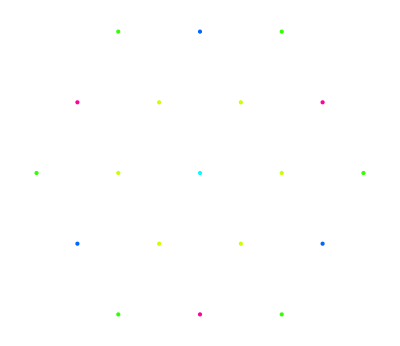

```mathematica
Graphics[GraphRepOrbitRootPoints2D[1,{2,2},{PointSize[Large],Hue[0.3*#1]}&]]
```

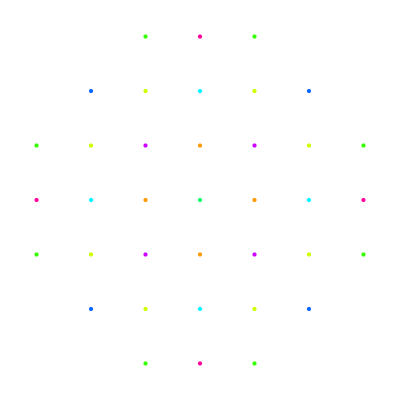

```mathematica
Graphics[GraphRepOrbitRootPoints2D[2,{2,2},{PointSize[Large],Hue[0.3*#1]}&]]
```

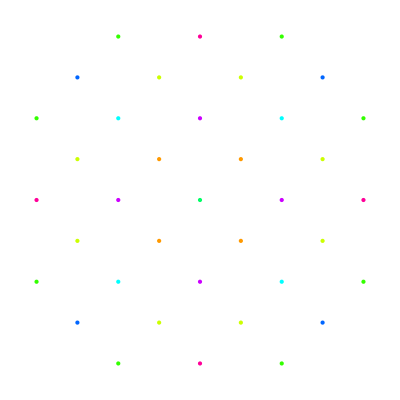

```mathematica
Graphics[GraphRepOrbitRootPoints2D[3,{2,2},{PointSize[Large],Hue[0.3*#1]}&]]
```

```mathematica
Graphics[GraphRepOrbitRootPoints2D[4,{2,2},{PointSize[Large],Hue[0.3*#1]}&]]
```

-Graphics-

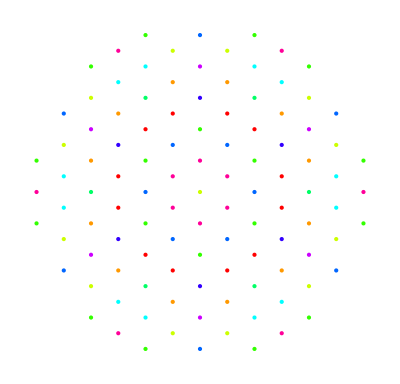

```mathematica
Graphics[GraphRepOrbitRootPoints2D[7,{2,2},{PointSize[Large],Hue[0.3*#1]}&]]
```

## Extras

### Canonical Root Vectors

```mathematica
CanonRootVectorMetScale[type_,vers_] := Module[{family,n},
{family,n} = type;
Switch[family,
1, Switch[vers,1,1,2,1/2],
2,1/2,
3,If[n>1,1,2],
4,1,
5,Switch[n,
6,Switch[vers,1,1,2,1,3,1,4,1,5,1/2],
7,Switch[vers,1,1,2,1,3,1],
8,Switch[vers,1,1,2,1]],
6,1/2,
7,Switch[vers,1,1,2,1/2]
]
]
```

```mathematica
TestCanonicalRootVectors[type_,vers_,metscale_] := Module[{la,cvc},
la = GetLieAlgebra[type];
If[la==BadValue,Return[BadValue]];
cvc = CanonicalRootVectors[type,vers];
ArrayRules[SparseArray[Expand[cvc.Transpose[cvc]] - metscale*la["Metric"]]]
]
```

```mathematica
TestCanonicalRootVectors[type_,vers_] := TestCanonicalRootVectors[type,vers,CanonRootVectorMetScale[type,vers]]
```

```mathematica
TestCanonicalRootVectors[type_] := Table[TestCanonicalRootVectors[type,vers],{vers,NumCanonRootVectors[type]}]
```

```mathematica
TestCRVClassical[n_] := Tally[Flatten[Table[TestCanonicalRootVectors[{f,n}],{f,1,If[n>1,4,3]}]]]
```

```mathematica
TestCRVExceptional[] := Tally[Flatten[Table[TestCanonicalRootVectors[type],{type,Partition[{7,2,6,4,5,6,5,7,5,8},2]}]]]
```

```mathematica
TestCRVClassical[1]
```

{{{_,_}→0,4}}

```mathematica
TestCRVClassical[5]
```

{{{_,_}→0,5}}

```mathematica
TestCRVExceptional[]
```

{{{_,_}→0,13}}

### Algebra Roots, Matrices Found Directly

```mathematica
PosRootsExplicitTest[type_] := Sort[PositiveRootsExplicit[type]] === Sort[First /@ (GetLieAlgebra[type]["PosRoots"])]
```

```mathematica
TestExplicit[what_,"Class",n_] := Table[what[{f,n}],{f,If[n>1,4,3]}]
```

```mathematica
TestExplicit[what_,"Except"] := Table[what[type],{type,Partition[{7,2,6,4,5,6,5,7,5,8},2]}]
```

```mathematica
TestExplicit[PosRootsExplicitTest,"Class",5]
```

{True,True,True,True}

```mathematica
MetricExplicitTest[type_] := MetricExplicit[type] === (GetLieAlgebra[type]["Metric"])
```

```mathematica
InverseMetricExplicitTest[type_] := InverseMetricExplicit[type] === (GetLieAlgebra[type]["InvMet"])
```

```mathematica
WeightSpaceMetricExplicitTest[type_] := WeightSpaceMetricExplicit[type] === (#.GetLieAlgebra[type]["Metric"].Transpose[#]& @ GetLieAlgebra[type]["InvCtn"])
```

```mathematica
InverseWeightSpaceMetricExplicitTest[type_] := InverseWeightSpaceMetricExplicit[type] === (Transpose[#].GetLieAlgebra[type]["InvMet"].#& @ GetLieAlgebra[type]["CtnMat"])
```

```mathematica
CartanMatrixExplicitTest[type_] := CartanMatrixExplicit[type] === (GetLieAlgebra[type]["CtnMat"])
```

```mathematica
InverseCartanMatrixExplicitTest[type_] := InverseCartanMatrixExplicit[type] === (GetLieAlgebra[type]["InvCtn"])
```

```mathematica
AllMatricesTest[type_] := Table[test[type],{test,{MetricExplicitTest,InverseMetricExplicitTest,WeightSpaceMetricExplicitTest,InverseWeightSpaceMetricExplicitTest,CartanMatrixExplicitTest,InverseCartanMatrixExplicitTest}}]
```

```mathematica
TestExplicit[AllMatricesTest,"Class",1]
```

{{True,True,True,True,True,True},{True,True,True,True,True,True},{True,True,True,True,True,True}}

```mathematica
TestExplicit[AllMatricesTest,"Class",7]
```

{{True,True,True,True,True,True},{True,True,True,True,True,True},{True,True,True,True,True,True},{True,True,True,True,True,True}}

```mathematica
TestExplicit[AllMatricesTest,"Except"]
```

{{True,True,True,True,True,True},{True,True,True,True,True,True},{True,True,True,True,True,True},{True,True,True,True,True,True},{True,True,True,True,True,True}}

### Total Degeneracies / Dimensions Found Explicitly

```mathematica
(* Numerical *)
```

```mathematica
TotalDegenExplicitTest[type_,maxwts_] := TotalDegenExplicit[type,maxwts]-TotalDegen[type,maxwts]
```

```mathematica
(* Symbolic *)
```

```mathematica
TotalDegenExplicitSymbTest[type_,w_] := Simplify[(TotalDegenExplicit[type,#,False]-TotalDegen[type,#,False])& @ Array[w,type[[2]]]]
```

```mathematica
TotalDegenExplicitSymbTest["Class",n_,w_] := Table[TotalDegenExplicitSymbTest[{f,n},w],{f,If[n>1,4,3]}]
```

```mathematica
TotalDegenExplicitSymbTest["Except",w_] := Table[TotalDegenExplicitSymbTest[type,w],{type,Partition[{7,2,6,4,5,6,5,7,5,8},2]}]
```

### Weyl Groups

```mathematica
(* Should be the same number *)
```

```mathematica
WeylGroupOrderTest[type_] := {GetWeylGroupOrder[type],Length[FillOutWeylGroup[type]]}
```

```mathematica
(* Alternative Weyl-orbit product *)
```

```mathematica
AltOrbitProductTest[type_,maxwts1_,maxwts2_] := {AltOrbitProduct[type,maxwts1,maxwts2],DecomposeOrbitProduct[type,maxwts1,maxwts2]}
```

### Cartan-Weyl Normalizations

```mathematica
First /@ GetLieAlgebra[{1,3}]["PosRoots"]
```

{{0,0,1},{0,1,0},{1,0,0},{0,1,1},{1,1,0},{1,1,1}}

```mathematica
CWNSolution[{1,3},TestCWNorm]
```

{TestCWNorm[{0,1,0},{0,0,1}]→1,TestCWNorm[{1,0,0},{0,1,0}]→1,TestCWNorm[{0,1,1},{1,0,0}]→1,TestCWNorm[{1,1,0},{0,0,1}]→-1}